```mathematica
SetOptions[{ParametricPlot,ListLinePlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLinearPlot,ListLogLogPlot,ListContourPlot,LogPlot,Plot,RegionPlot,ContourPlot},Frame->True,BaseStyle->{FontColor->Black,FontWeight->"Normal",FontSize->16,FontFamily->"Times"},Axes->False,PlotLegends->Automatic,AspectRatio->1,ImageSize->500,AspectRatio->1/GoldenRatio,PlotRange->Full,GridLines->Automatic];
colours=ColorData[97,"ColorList"];
```

```mathematica
Exp[-1.]
```

0.367879

# Finite temperature functions

```mathematica
Clear[JB];
JB[mt2_]:=If[mt2>=0,
IntegralJPositiveMass=NIntegrate[x^2Log[1-Exp[-√(x^2+mt2)]],{x,0,Infinity},WorkingPrecision->15];
Joutput=IntegralJPositiveMass;
Joutput,
(**IntegralJReal1=NIntegrate[x^2Log[1-Exp[-√(x^2-Abs[mt2])]],{x,Abs[mt2],Infinity},WorkingPrecision->10];
IntegralJReal2=NIntegrate[Re[x^2Log[1-Cos[√(x^2-Abs[mt2])]]],{x,0,√Abs[mt2]},WorkingPrecision->10];**)IntegralJReal1=NIntegrate[x^2Log[1-Exp[-√(x^2-Abs[mt2])]],{x,√Abs[mt2],Infinity},WorkingPrecision->10];IntegralJReal2=NIntegrate[x^2  Log[√(2(1-Cos[√(Abs[mt2]-x^2)]))],{x,0,√Abs[mt2]},WorkingPrecision->100];
(*IntegralJImaginary=Integrate[x^2 ArcTan[Sin[√(Abs[mt2]-x^2)]/(1-Cos[√(Abs[mt2]-x^2)])],{x,0,√Abs[mt2]}];*)
Joutput=Total[Re[{IntegralJReal1,IntegralJReal2}]];
Joutput=IntegralJReal1+IntegralJReal2];
JBlist=Table[{m2,JB[m2]},{m2,-10,1000}];JBinterpolated=Interpolation[JBlist];
```

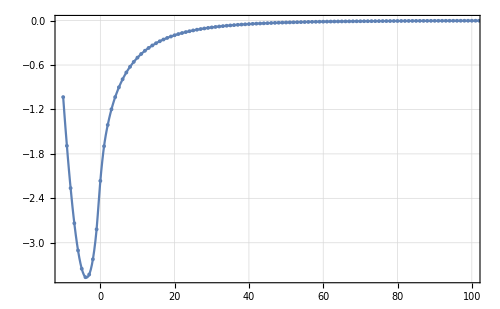

```mathematica
Show[Plot[JBinterpolated[m2],{m2,Min[Transpose[JBlist][[1]]],Max[Transpose[JBlist][[1]]]},PlotRange->{{-10,100},All}],ListPlot[JBlist]]
```

```mathematica
Jmin=NMinimize[Re[JBinterpolated[m2]],{m2}];JBspline[m2_]:=If[m2>-3.7224781307403183,JBinterpolated[m2],Jmin[[1]]];
```

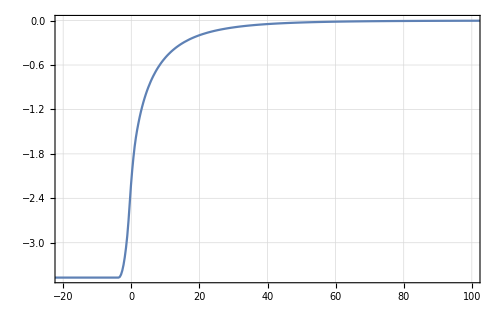

```mathematica
Plot[JBspline[m2],{m2,-100,1000},PlotRange->{{-20,100},All}]
```

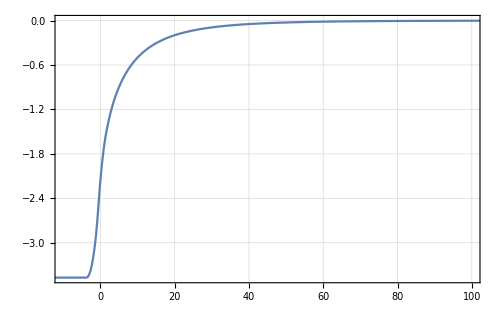

```mathematica
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/JB_spline.dat",Re[JBlist]]
```

/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/JB_spline.dat

```mathematica
JBData=Import["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/JB_spline.dat","Table"];
```

# Higgs Trilinear

```mathematica
ClearAll["Global`*"]
```

```mathematica
Vh[h_]:=-m^2/2(h+v)^2+λ/4(h+v)^4
```

```mathematica
Clear[λ];
λ=λ/.Solve[Evaluate[D[Vh[h],{h,1}]/.{h->0}]==0,λ][[1]];
```

```mathematica
Evaluate[D[Vh[h],{h,2}]/.{h->0}]
```

mh^2

```mathematica
m=mh/√2;
```

```mathematica
D[Vh[h],{h,3}]/.{h->0}
```

(3 mh^2)/v

# Gegenbauer paper

```mathematica
ClearAll["Global`*"]
```

```mathematica
Npi=2;(*Number of Goldstones!!*)
pivec=Table[pi[i],{i,1,Npi}];
Pinorm=√(pivec.pivec);
gmetric=Sin[Pinorm/f]^2 f^2/Pinorm^2 Table[KroneckerDelta[a,b]+pi[a]pi[b]/Pinorm^2((Pinorm^2/f^2)Csc[Pinorm/f]^2-1),{a,1,Npi},{b,Npi}];
gmetricinverse=1/(Sin[Pinorm/f]^2) Pinorm^2 /f^2Table[KroneckerDelta[a,b]-pi[a]pi[b]/Pinorm^2(1-f^2/Pinorm^2 Sin[Pinorm/f]^2),{a,1,Npi},{b,Npi}];
Print["Check g times g^-1"]
Print[MatrixForm[FullSimplify[gmetric.gmetricinverse]]];
dgilk=Hold[Sum[gmetricinverse[[i,m]](D[gmetric[[l,m]],pi[k]]+D[gmetric[[k,m]],pi[l]]-D[gmetric[[l,k]],pi[m]]),{m,1,Npi}]];Christoffel=1/2Table[ReleaseHold[dgilk],{i,1,Npi},{l,1,Npi},{k,1,Npi}];
Potential=G[Pinorm];
gD2V=Hold[Sum[gmetricinverse[[i,k]]D[Potential,pi[k],pi[j]],{k,1,Npi}]];
gGamDV=Hold[Sum[gmetricinverse[[i,l]] Christoffel[[m,j,l]]D[Potential,pi[m]],{m,1,Npi},{l,1,Npi}]];MassMatrix=Table[ReleaseHold[gD2V-gGamDV],{i,1,Npi},{j,1,Npi}];
```

Check g times g^-1

(1 | 0
0 | 1)

```mathematica
(*Γ=FullSimplify[Christoffel/.Table[pi[i]->0,{i,2,Npi}]/.{pi[1]->Π}];
ginv=FullSimplify[gmetricinverse/.Table[pi[i]->0,{i,2,Npi}]/.{pi[1]->Π}];
MatrixForm[FullSimplify[ginv.{{xx,0},{0,0}}-ginv.(Γ.{y,0})]]*)
```

```mathematica
Riemantensor[α_,β_,γ_,δ_]:=Hold[D[Christoffel[[α,β,δ]],pi[γ]]-D[Christoffel[[α,β,γ]],pi[δ]]+Sum[Christoffel[[μ,β,δ]]Christoffel[[α,μ,γ]]-Christoffel[[μ,β,γ]]Christoffel[[α,μ,δ]],{μ,1,Npi}]];
RiemantensorMatrix=Table[ReleaseHold[Riemantensor[α,β,γ,δ]],{α,1,Npi},{β,1,Npi},{γ,1,Npi},{δ,1,Npi}];RicciCurvatureTensor=Hold[Sum[RiemantensorMatrix[[λ]][[μ]][[λ]][[κ]],{λ,1,Npi}]];
RicciCurvatureTensorMatrix=Table[ReleaseHold[RicciCurvatureTensor],{μ,1,Npi},{κ,1,Npi}];CurvatureScalar=FullSimplify[Tr[gmetricinverse.RicciCurvatureTensorMatrix]];
```

```mathematica
CurvatureScalar
```

2/f^2

```mathematica
Replace[ FullSimplify[Tr[MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(-F^2+Sum[pi[i]^2,{i,1,Npi}])->-F^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

(Cot[(√(Π^2))/f] G'[√(Π^2)])/f+G''[√(Π^2)]

```mathematica
EigenMasses=FullSimplify[Replace[MassMatrix/.Table[pi[i]->0,{i,2,Npi}],{pi[1]->Π},All]];EigenMasses
```

{{G''[√(Π^2)],0},{0,(Cot[(√(Π^2))/f] G'[√(Π^2)])/f}}

```mathematica
MatrixForm[EigenMasses]
```

(G''[√(Π^2)] | 0
0 | (Cot[(√(Π^2))/f] G'[√(Π^2)])/f)

```mathematica
pivecST=Table[Dpi[i],{i,1,Npi}];
index=1;
EOMindex=Sum[Christoffel[[index,j,k]]pivecST[[j]]pivecST[[k]] ,{j,1,Npi},{k,1,Npi}]-Sum[D[Potential,pi[j]]gmetricinverse[[index,j]],{j,1,Npi}];FullSimplify[Replace[EOMindex/.Join[Table[pi[i]->0,{i,2,Npi}],Table[Dpi[i]->0,{i,2,Npi}]],{pi[1]->Π,Dpi[1]->Π'},All],Π>0]
```

-G'[Π]

```mathematica
FullSimplify[Det[gmetricinverse]]
```

(Csc[(√(pi[1]^2+pi[2]^2))/f]^2 (pi[1]^2+pi[2]^2))/f^2

```mathematica
Replace[ FullSimplify[Tr[MassMatrix.MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(-F^2+Sum[pi[i]^2,{i,1,Npi}])->-F^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

(3 Cot[(√(Π^2))/f]^2 G'[√(Π^2)]^2)/f^2+G''[√(Π^2)]^2

# Flat Field-space metric

```mathematica
ClearAll["Global`*"]
```

```mathematica
Npi=4;(*Number of Goldstones!!*)
pivec=Table[pi[i],{i,1,Npi}];
Pinorm=√(pivec.pivec);
gmetric=IdentityMatrix[Npi];
gmetricinverse=IdentityMatrix[Npi];
Print["Check g times g^-1"]
Print[MatrixForm[FullSimplify[gmetric.gmetricinverse]]];
dgilk=Hold[Sum[gmetricinverse[[i,m]](D[gmetric[[l,m]],pi[k]]+D[gmetric[[k,m]],pi[l]]-D[gmetric[[l,k]],pi[m]]),{m,1,Npi}]];Christoffel=1/2Table[ReleaseHold[dgilk],{i,1,Npi},{l,1,Npi},{k,1,Npi}];
Potential=G[Pinorm];
gD2V=Hold[Sum[gmetricinverse[[i,k]]D[Potential,pi[k],pi[j]],{k,1,Npi}]];
gGamDV=Hold[Sum[gmetricinverse[[i,l]] Christoffel[[m,j,l]]D[Potential,pi[m]],{m,1,Npi},{l,1,Npi}]];MassMatrix=Table[ReleaseHold[gD2V-gGamDV],{i,1,Npi},{j,1,Npi}];
```

Check g times g^-1

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Replace[ FullSimplify[Tr[MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(-F^2+Sum[pi[i]^2,{i,1,Npi}])->-F^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

(3 Cot[(√(Π^2))/f] G'[√(Π^2)])/f+G''[√(Π^2)]

```mathematica
DSolve[{4 G'[x]/x+G''[x]==-A G[x]},G[x],x]
```

{{G[x]→(√(2/π) C[2] (-Cos[√A x]/(√A x)-Sin[√A x]))/(x^(3/2) √(√A x))+(√(2/π) C[1] (-Cos[√A x]+Sin[√A x]/(√A x)))/(x^(3/2) √(√A x))}}

```mathematica
?GegenbauerC
```

```mathematica
GegenbauerC[1,(Npi-1)/2,Cos[x]]+Cos[x]^2 Log[Abs[C]]
```

-2+12 Cos[x]^2

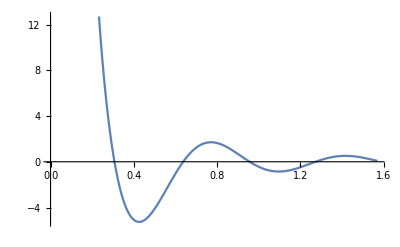

```mathematica
c1=1;c2=-4;A=100;Plot[(√(2/π) c2 (-Cos[√A x]/(√A x)-Sin[√A x]))/(x^(3/2) √(√A x))+(√(2/π) c1 (-Cos[√A x]+Sin[√A x]/(√A x)))/(x^(3/2) √(√A x)),{x,0,π/2}]
```

```mathematica
Manipulate[Plot[(√(2/π) c2 (-Cos[√A x]/(√A x)-Sin[√A x]))/(x^(3/2) √(√A x))+(√(2/π) c1 (-Cos[√A x]+Sin[√A x]/(√A x)))/(x^(3/2) √(√A x)),{x,0,π/2}],{ c2,-1,1},{ c1,-1,1},{A,-2,2}]
```

```mathematica
EigenMasses=FullSimplify[Replace[MassMatrix/.Table[pi[i]->0,{i,2,Npi}],{pi[1]->Π},All]];EigenMasses
```

{{G''[√(Π^2)],0,0,0,0},{0,(Cot[(√(Π^2))/f] G'[√(Π^2)])/f,0,0,0},{0,0,(Cot[(√(Π^2))/f] G'[√(Π^2)])/f,0,0},{0,0,0,(Cot[(√(Π^2))/f] G'[√(Π^2)])/f,0},{0,0,0,0,(Cot[(√(Π^2))/f] G'[√(Π^2)])/f}}

```mathematica
pivecST=Table[Dpi[i],{i,1,Npi}];
index=1;
EOMindex=Sum[Christoffel[[index,j,k]]pivecST[[j]]pivecST[[k]] ,{j,1,Npi},{k,1,Npi}]-Sum[D[Potential,pi[j]]gmetricinverse[[index,j]],{j,1,Npi}];FullSimplify[Replace[EOMindex/.Join[Table[pi[i]->0,{i,2,Npi}],Table[Dpi[i]->0,{i,2,Npi}]],{pi[1]->Π,Dpi[1]->Π'},All],Π>0]
```

-G'[Π]

```mathematica
FullSimplify[Det[gmetricinverse]]
```

(Csc[(√(pi[1]^2+pi[2]^2))/f]^2 (pi[1]^2+pi[2]^2))/f^2

```mathematica
Replace[ FullSimplify[Tr[MassMatrix.MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(-F^2+Sum[pi[i]^2,{i,1,Npi}])->-F^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

(2 Cot[(√(Π^2))/f]^2 G'[(√(Π^2))/f]^2+G''[(√(Π^2))/f]^2)/f^4

# Gegenbauer Plots

```mathematica
ClearAll["Global`*"]
```

```mathematica
DSolve[{G''[x]+2λ Cot[x]G'[x]+cc G[x]==0},G[x],x]
```

{{G[x]→C[1] (-1+Cos[x]^2)^(1/4 (1-2 λ)) LegendreP[1/2 (-1+2 √(cc+λ^2)),1/2 (-1+2 λ),Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4 (1-2 λ)) LegendreQ[1/2 (-1+2 √(cc+λ^2)),1/2 (-1+2 λ),Cos[x]]}}

```mathematica
DSolve[{G''[x]+2λ Cot[x]G'[x]+n(n+2λ)G[x]==0},G[x],x]
```

{{G[x]→C[1] (-1+Cos[x]^2)^(1/4 (1-2 λ)) LegendreP[1/2 (-1+2 n+2 λ),1/2 (-1+2 λ),Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4 (1-2 λ)) LegendreQ[1/2 (-1+2 n+2 λ),1/2 (-1+2 λ),Cos[x]]}}

```mathematica
NN=4;n=21;λ=(NN-1)/2;sol=DSolve[{G''[x]+2λ Cot[x]G'[x]+n(n+2λ)G[x]==0},G[x],x];
```

```mathematica
Gegenbauer1[xx_?NumericQ]:=(G[x]/.(sol[[1]]/.{C[2]->0,C[1]->1}))/.{x->xx};Gegenbauer2[xx_?NumericQ]:=(G[x]/.(sol[[1]]/.{C[2]->1,C[1]->0}))/.{x->xx};
```

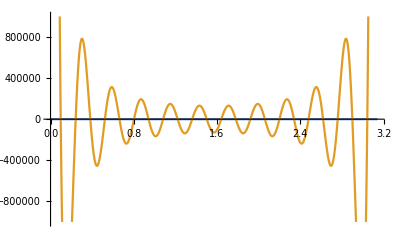

```mathematica
Plot[{Gegenbauer1[x],Gegenbauer2[x]},{x,0,π},PlotRange->{-10^6,10^6}]
```

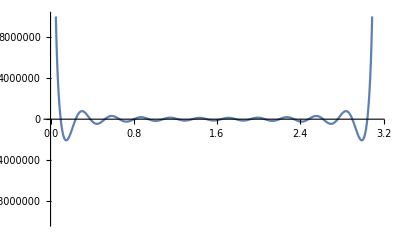
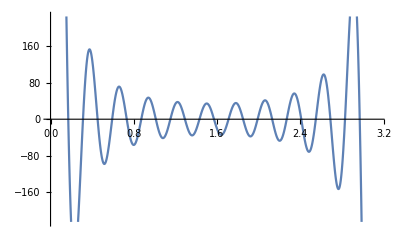

```mathematica
{Plot[Gegenbauer2[x],{x,0,π},PlotRange->{-10^7,10^7}],Plot[10^8Gegenbauer1[x],{x,0,π}]}
```

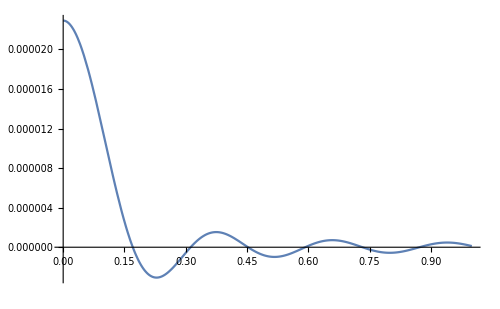

```mathematica
Plot[Gegenbauer1[x],{x,0,1},PlotRange->All]
```

```mathematica
NMinimize[{Gegenbauer1[x],x>0},x]
```

{-0.0000229241,{x→3.14159}}

```mathematica
5.1/n
```

0.242857

```mathematica
GegebauerPlot[Ngb_,n_]:=Module[{λ=(Ngb-1)/2},
sol=DSolve[{G''[x]+2λ Cot[x]G'[x]+n(n+2λ)G[x]==0},G[x],x];
Gegenbauer1[z_]:=(G[x]/.(sol[[1]]/.{C[2]->0,C[1]->1}))/.{x->z};
plot=Plot[Gegenbauer1[z],{z,0,1},PlotRange->All];
Return[plot]];
```

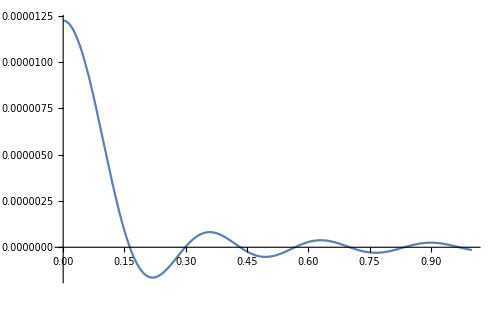

```mathematica
GegebauerPlot[4,22]
```

```mathematica
GegebauerPotential[Ngb_,n_,z_]:=Module[{λ=(Ngb-1)/2},
sol=DSolve[{G''[x]+2λ Cot[x]G'[x]+n(n+2λ)G[x]==0},G[x],x];
Output=(G[x]/.(sol[[1]]/.{C[2]->0,C[1]->1}))/.{x->z};
Return[Output]];
TrilinearHiggs[Ngb_,n_]:=Module[{mh=125,
v=246},
chhhSM=3 mh^2/v;
xmin=x/.NMinimize[{GegebauerPotential[Ngb,n,x],x>0,x<1},x][[2]];
f=v/xmin;
constant=mh^2/D[GegebauerPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->v};chhh=constant D[GegebauerPotential[Ngb,n,ϕ/f],{ϕ,3}]/.{ϕ->v};
Return[chhh/chhhSM]]TrilinearCouplingsList=Table[{i,TrilinearHiggs[4,i]},{i,2,31,2}];plotInSpherical=ListPlot[TrilinearCouplingsList,PlotRange->{-1,0},FrameLabel->{"x","c_hhh/c_hhh^SM"},Joined->True]
```

ListPlot::lpn: TrilinearCouplingsList is not a list of numbers or pairs of numbers.

ListPlot[TrilinearCouplingsList,PlotRange→{-1,0},FrameLabel→{x,c_hhh/c_hhh^SM},Joined→True]

# Square root parametrization

```mathematica
ClearAll["Global`*"]
```

```mathematica
Npi=4;
pivec=Table[pi[i],{i,1,Npi}];
Pinorm=√(pivec.pivec);
gmetric=Table[KroneckerDelta[a,b]+pi[a]pi[b]/(F^2-pivec.pivec),{a,1,Npi},{b,Npi}];gmetricinverse=Table[KroneckerDelta[a,b]-pi[a]pi[b]/F^2,{a,1,Npi},{b,Npi}];
Print["Check g times g^-1"]
MatrixForm[FullSimplify[gmetric.gmetricinverse]]
dgilk=Hold[Sum[gmetricinverse[[i,m]](D[gmetric[[l,m]],pi[k]]+D[gmetric[[k,m]],pi[l]]-D[gmetric[[l,k]],pi[m]]),{m,1,Npi}]];Christoffel=1/2Table[ReleaseHold[dgilk],{i,1,Npi},{l,1,Npi},{k,1,Npi}];
Potential=-c √(F^2-pivec.pivec);
Potential=G[Pinorm];
gD2V=Hold[Sum[gmetricinverse[[i,k]]D[Potential,pi[k],pi[j]],{k,1,Npi}]];
gGamDV=Hold[Sum[gmetricinverse[[i,l]] Christoffel[[m,j,l]]D[Potential,pi[m]],{m,1,Npi},{l,1,Npi}]];MassMatrix=Table[ReleaseHold[gD2V-gGamDV],{i,1,Npi},{j,1,Npi}];
```

Check g times g^-1

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Gamma1[a_,b_,c_]:=(dgilk/.{i->a,l->b,k->c});
Riemantensor[α_,β_,γ_,δ_]:=Hold[D[Christoffel[[α,β,δ]],pi[γ]]-D[Christoffel[[α,β,γ]],pi[δ]]+Sum[Christoffel[[μ,β,δ]]Christoffel[[α,μ,γ]]-Christoffel[[μ,β,γ]]Christoffel[[α,μ,δ]],{μ,1,Npi}]];
RiemantensorMatrix=Table[ReleaseHold[Riemantensor[α,β,γ,δ]],{α,1,Npi},{β,1,Npi},{γ,1,Npi},{δ,1,Npi}];RicciCurvatureTensor=Hold[Sum[RiemantensorMatrix[[λ]][[μ]][[λ]][[κ]],{λ,1,Npi}]];
RicciCurvatureTensorMatrix=Table[ReleaseHold[RicciCurvatureTensor],{μ,1,Npi},{κ,1,Npi}];CurvatureScalar=FullSimplify[Tr[gmetricinverse.RicciCurvatureTensorMatrix]];
```

```mathematica
CurvatureScalar
```

12/F^2

```mathematica
Replace[FullSimplify[Tr[MassMatrix.MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(-F^2+Sum[pi[i]^2,{i,1,Npi}])->-F^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

(((3 F^4-6 F^2 Π^2+4 Π^4) G'[√(Π^2)]^2)/Π^2+2 √(Π^2) (-F^2+Π^2) G'[√(Π^2)] G''[√(Π^2)]+(-F^2+Π^2)^2 G''[√(Π^2)]^2)/F^4

```mathematica
EigenMasses=FullSimplify[Replace[MassMatrix/.Table[pi[i]->0,{i,2,Npi}],{pi[1]->Π},All]];EigenMasses
```

{{(-√(Π^2) G'[√(Π^2)]+(F-Π) (F+Π) G''[√(Π^2)])/F^2,0,0,0},{0,((F-Π) (F+Π) G'[√(Π^2)])/(F^2 √(Π^2)),0,0},{0,0,((F-Π) (F+Π) G'[√(Π^2)])/(F^2 √(Π^2)),0},{0,0,0,((F-Π) (F+Π) G'[√(Π^2)])/(F^2 √(Π^2))}}

```mathematica
FullSimplify[Tr[EigenMasses]]
```

(((3 F^3-4 F Π^2) G'[(√(Π^2))/F])/(√(Π^2))+(F-Π) (F+Π) G''[(√(Π^2))/F])/F^4

```mathematica
Replace[FullSimplify[Tr[MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(-F^2+Sum[pi[i]^2,{i,1,Npi}])->-F^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

(((3 F^2-4 Π^2) G'[√(Π^2)])/(√(Π^2))-(-F^2+Π^2) G''[√(Π^2)])/F^2

```mathematica
Replace[FullSimplify[Det[MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(F^2-Sum[pi[i]^2,{i,1,Npi}])->F^2-Π^2,(-F^2+Sum[pi[i]^2,{i,1,Npi}])->-F^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

((F^2-Π^2) G'[√(Π^2)] (-Π^2 G'[√(Π^2)]-√(Π^2) (-F^2+Π^2) G''[√(Π^2)]))/(F^4 Π^2)

```mathematica
pivecST=Table[Dpi[i],{i,1,Npi}];
index=1;
EOMindex=Sum[Christoffel[[index,j,k]]pivecST[[j]]pivecST[[k]] ,{j,1,Npi},{k,1,Npi}]-Sum[D[Potential,pi[j]]gmetricinverse[[index,j]],{j,1,Npi}];FullSimplify[Replace[EOMindex/.Join[Table[pi[i]->0,{i,2,Npi}],Table[Dpi[i]->0,{i,2,Npi}]],{pi[1]->Π,Dpi[1]->Π'},All],Π>0]
```

(Π (Π')^2)/(F^2-Π^2)+(-1+Π^2/F^2) G'[Π]

```mathematica
Replace[FullSimplify[Tr[(MassMatrix.MassMatrix).MatrixLog[MassMatrix/Λ^2]]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(F^2-Sum[pi[i]^2,{i,1,Npi}])->F^2-Π^2,(-F^2+Sum[pi[i]^2,{i,1,Npi}])->-F^2+Π^2,Sum[pi[i]^2,{i,1,Npi}]->Π^2},All]
```

$Aborted

```mathematica
SomeMatrix={{100,10},{10,150}};
soleigh=Eigensystem[SomeMatrix];
{m1,m2}=soleigh[[1]];
μscale=100;
Rot={Normalize[soleigh[[2]][[1]]],Normalize[soleigh[[2]][[2]]]};
Mdiag=FullSimplify[Rot.SomeMatrix.Transpose[Rot]];
MatrixForm[SomeMatrix]
```

(100 | 10
10 | 150)

```mathematica
FullSimplify[Tr[(Mdiag.Mdiag).MatrixLog[Mdiag/μscale]]-(m1^2Log[m1/μscale]+m2^2Log[m2/μscale])]
```

0

Non linear transformation of the pion fields

```mathematica
nvec=Join[pivec,{√(1-pivec.pivec)}];
```

```mathematica
nvec.nvec
```

1

```mathematica
Rrotx={{1,0,0},{0,Cos[α],Sin[α]},{0,-Sin[α],Cos[α]}};
Rroty={{Cos[α],0,Sin[α]},{0,1,0},{-Sin[α],0,Cos[α]}};
Rrotz={{Cos[α],Sin[α],0},{-Sin[α],Cos[α],0},{0,0,1}};
```

```mathematica
(Rroty.nvec)
```

{Cos[α] pi[1]+√(1-pi[1]^2-pi[2]^2) Sin[α],pi[2],Cos[α] √(1-pi[1]^2-pi[2]^2)-pi[1] Sin[α]}

```mathematica
constant=FullSimplify[-4n^2-4n λ];
Ngb=2λ+1;
Print[constant];FullSimplify[DSolve[{G''[Π](-Π^2+F^2)+G'[Π]((Ngb-1)F^2-Ngb Π^2)/Π==constant G[Π]},G[Π],Π]]
```

-4 n (n+λ)

{{G[Π]→C[1] Hypergeometric2F1[-n,n+λ,1/2+λ,Π^2/F^2]+ⅈ^(1-2 λ) F^(-1+2 λ) Π^(1-2 λ) C[2] Hypergeometric2F1[1/2+n,1/2-n-λ,3/2-λ,Π^2/F^2]}}

```mathematica
constant=FullSimplify[λ^2-n^2];
Ngb=2λ+1;
Print[constant];FullSimplify[DSolve[{G''[Π](-Π^2+F^2)+G'[Π]((Ngb-1)F^2-Ngb Π^2)/Π==constant G[Π]},G[Π],Π]]
```

-n^2+λ^2

{{G[Π]→ⅈ^(1-2 λ) F^(-1+2 λ) Π^(1-2 λ) C[2] Hypergeometric2F1[1/2 (1-n-λ),1/2 (1+n-λ),3/2-λ,Π^2/F^2]+C[1] Hypergeometric2F1[1/2 (-n+λ),(n+λ)/2,1/2+λ,Π^2/F^2]}}

```mathematica
constant=FullSimplify[-n^2-2λ n];
Ngb=2λ+1;
Print[constant];FullSimplify[DSolve[{G''[Π](-Π^2+1^2)+G'[Π]((Ngb-1)-Ngb Π^2)/Π==constant G[Π]},G[Π],Π]]
```

-n (n+2 λ)

{{G[Π]→C[1] Hypergeometric2F1[-n/2,n/2+λ,1/2+λ,Π^2]+ⅈ^(1-2 λ) Π^(1-2 λ) C[2] Hypergeometric2F1[(1+n)/2,1/2 (1-n-2 λ),3/2-λ,Π^2]}}

```mathematica
PotentialOutput[F_?NumberQ,Ngb_?NumberQ,x_?NumberQ]:=Module[{},
Print["Selecting the following numerical values"];Print["F=",F,", Ngb=",Ngb,", x=",x];Print["Evaluating the Hypergeometric function F(a,b,c,Π/F), where"];
Print["a=",1/4 (-1+Ngb-2 x),", b=",1/4 (-1+Ngb+2 x),", c=",Ngb/2];
plot1=Plot[Hypergeometric2F1[1/4 (-1+Ngb-2 x),1/4 (-1+Ngb+2 x),Ngb/2,ϕ^2/F^2],{ϕ,0,F},AxesLabel->{"Π/F","G(Π/F)"},PlotRange->All];
Return[plot1]
]
```

Selecting the following numerical values

F=100, Ngb=4, x=1

Evaluating the Hypergeometric function F(a,b,c,Π/F), where

a=1/4, b=5/4, c=2

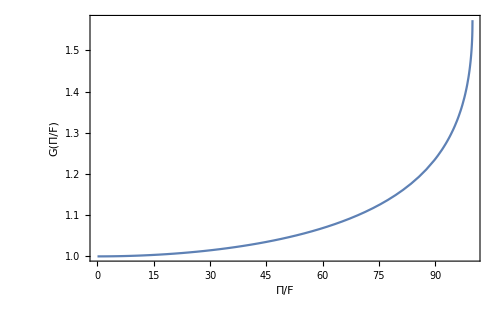

```mathematica
PotentialOutput[100,4,1]
```

```mathematica
Clear[GBPotential];GBPotential[Ngb_?NumberQ,x_?NumberQ,z_]:=Module[{λ=(Ngb-1)/2},(*Return[Hypergeometric2F1[1/4 (-1+Ngb-2 x),1/4 (-1+Ngb+2 x),Ngb/2,z^2]]*)Return[Hypergeometric2F1[-x/2,x/2+λ,λ+1/2,z^2]]
]
```

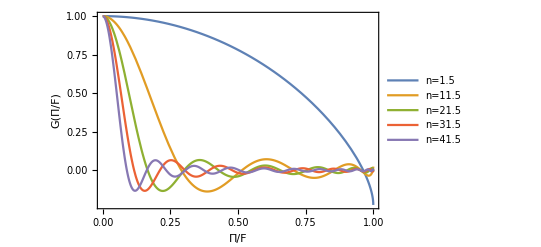

```mathematica
{legends,funcions}=Transpose[Table[{StringJoin["n=",ToString[i]],GBPotential[4,i,z]},{i,1.5,50,10}]];aplot=Plot[funcions,{z,0,1},(*AxesLabel->{"Π/F","G(Π/F)"},Axes->True*)Frame->True,FrameLabel->{"Π/F","G(Π/F)"},PlotLegends->legends]
```

```mathematica
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/hypergeometric.pdf",aplot]
```

/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/hypergeometric.pdf

```mathematica
Solve[-2==Ngb-1-2x,x]
```

{{x→(1+Ngb)/2}}

```mathematica
Append[Table[GBPotential[i,(1+i)/2,z],{i,1,15,1}],√(1-ϕ^2)]
```

{√(1-z^2),√(1-z^2),√(1-z^2),√(1-z^2),√(1-z^2),√(1-z^2),√(1-z^2),√(1-z^2),√(1-z^2),√(1-z^2),√(1-z^2),√(1-z^2),√(1-z^2),√(1-z^2),√(1-z^2),√(1-ϕ^2)}

```mathematica
TrilinearHiggs[Ngb_,n_]:=Module[{mh=125,
v=246},
chhhSM=3 mh^2/v;
xmin=x/.NMinimize[{GBPotential[Ngb,n,x],x>0,x<1},x][[2]];
f=v/xmin;
constant=mh^2/(D[GBPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->v});
chhh=constant Re[D[GBPotential[Ngb,n,ϕ/f],{ϕ,3}]/.{ϕ->v}];
Return[chhh/chhhSM]]
```

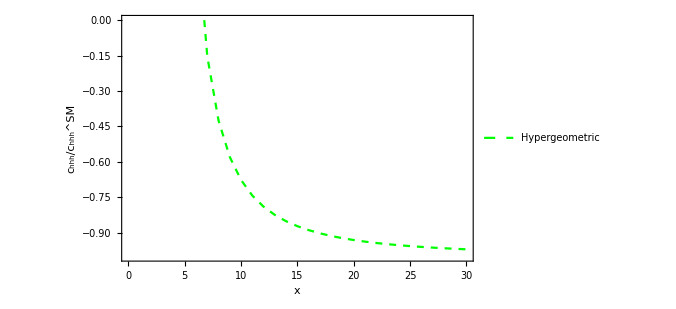

```mathematica
TrilinearCouplingsList=Table[{i,TrilinearHiggs[4,i]},{i,2,30,1}];plotInSquareRoot=ListPlot[TrilinearCouplingsList,Frame->True,FrameLabel->{"x","c_hhh/c_hhh^SM"},PlotStyle->{Green,Dashed},PlotLegends->Placed[{"Hypergeometric"},{.7,.7}],Joined->True,PlotRange->{-1,0}]
```

```mathematica
ClearAll["Global`*"];GBPotential[Ngb_?NumberQ,x_?NumberQ,z_]:=Module[{},Return[Hypergeometric2F1[1/4 (-1+Ngb-2 x),1/4 (-1+Ngb+2 x),Ngb/2,z^2]]
];
TrilinearHiggs[Ngb_,n_]:=Module[{mh=125,
v=246},
chhhSM=3 mh^2/v;
xmin1=x/.NMinimize[{GBPotential[Ngb,n,x],x>0,x<1},x][[2]];
xmin2=x/.FindMinimum[{GBPotential[Ngb,n,x],x>0,x<1},{x,0.}][[2]];xmin=Min[xmin1,xmin2];
f=v/xmin;
constant=mh^2/(D[GBPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->v});
chhh=constant Re[D[GBPotential[Ngb,n,ϕ/f],{ϕ,3}]/.{ϕ->v}];
Return[chhh/chhhSM]];
JBData=Import["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/JB_spline.dat","Table"];
JBinterpolated=Interpolation[JBData];
Jmin=NMinimize[JBinterpolated[m2],{m2}];JBspline[m2_]:=If[m2>-3.7224781307403183,JBinterpolated[m2],Jmin[[1]]];
```

```mathematica
Ngb=4;n=45;v=246;
Print["c_hhh/c_hhh^SM=",TrilinearHiggs[Ngb,n]];
```

c_hhh/c_hhh^SM=-0.986853

f=2159.55 GeV

The GB mass is given by 125.GeV

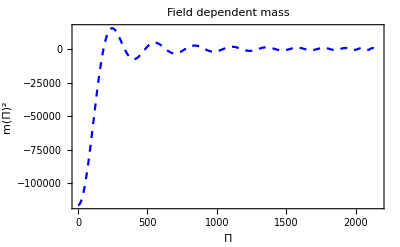
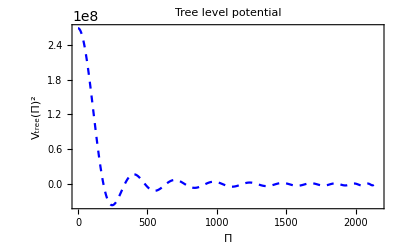

```mathematica
Print["f=",f," GeV"]
V0[ϕ_]:=constant GBPotential[Ngb,n,ϕ/f];
fieldDependentMasses[h_]:=((Ngb-1)^2/4-n^2)V0[h]/f^2;
VfiniteT[h_,T_]:=If[T==0,0,T^4/2/π^2JBspline[fieldDependentMasses[h]/T^2]]
Print["The GB mass is given by ",(D[constant GBPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->246})^.5, "GeV"];
plot1=Plot[fieldDependentMasses[h],{h,0,f},Frame->True,FrameLabel->{"Π","m(Π)^2"},PlotStyle->{Blue,Dashed},PlotLabel->"Field dependent mass",PlotRange->All];plot2=Plot[V0[ϕ],{ϕ,0,f},Frame->True,FrameLabel->{"Π","V_tree(Π)^2"},PlotStyle->{Blue,Dashed},PlotLabel->"Tree level potential",PlotRange->All];
{plot1,plot2}
```

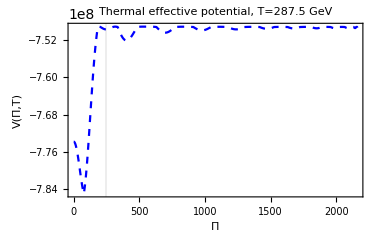

```mathematica
Temp=267.5+20 ;Plot[V0[h]+VfiniteT[h,Temp],{h,0,f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{v},{}},PlotRange->All]
```

Trying to find out temperature or symmetry restoration. First we need to define getphases  type of function

```mathematica
findMinimaAtT[T_]:=Module[{},
AllMinimaAtT=Quiet[Table[FindMinimum[{V0[h]+VfiniteT[h,T]},{h,h0},Method->"PrincipalAxis",WorkingPrecision->30],{h0,1,300,70}]];AllMinimaAtT=DeleteDuplicates[Round[(h/.{Transpose[AllMinimaAtT][[2]]})[[1]],.1]];
(*Print["Found minima at h = ",AllMinimaAtT];*)
eliminate={};For[i=1,i<=Length[AllMinimaAtT],i++,If[(AllMinimaAtT[[i]]<=300&&AllMinimaAtT[[i]]>=0),,AppendTo[eliminate,i]]];
AllMinimaAtT=Delete[AllMinimaAtT,Transpose[{eliminate}]];
(*Print["Selecting only minima at h = ",AllMinimaAtT];*)
Return[ReverseSort[AllMinimaAtT]]]
```

```mathematica
findMinimaAtT[Temp]
```

{246.,77.}

```mathematica
AllMinimaAtT
```

{77.,246.}

```mathematica
D[VfiniteT[h,Temp],{h,1}]/.{h->AllMinimaAtT[[1]]}
```

1.96289×10^6

```mathematica
allPhases={{},{}};
Do[minima=findMinimaAtT[T];For[i=1,i<=Length[minima],i++,If[i==1,AppendTo[allPhases[[1]],{T,minima[[i]]}],AppendTo[allPhases[[2]],{T,minima[[i]]}]]];,{T,200,400,1}];
```

```mathematica
For[i=1,i<Length[allPhases[[1]]],i++,Trestored=Transpose[allPhases[[1]]][[1]][[i]];If[Transpose[allPhases[[1]]][[2]][[i]]<10^(-4),Print["Temperature is restored at T=",Trestored," GeV"];Break[]]];
```

Temperature is restored at T=311 GeV

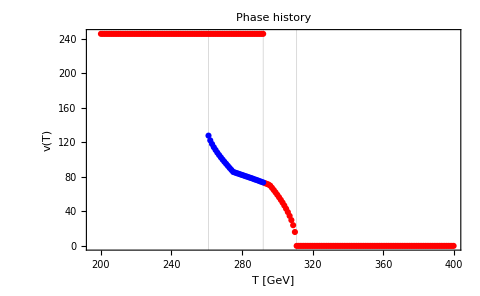

```mathematica
ListPlot[{allPhases[[1]],allPhases[[2]]},Frame->True,FrameLabel->{"T [GeV]","v(T)"},PlotStyle->{Red,Blue,Dashed},PlotLabel->StringJoin["Phase history" ],PlotRange->All,GridLines->{{Trestored,Transpose[allPhases[[2]]][[1]][[-1]],Transpose[allPhases[[2]]][[1]][[1]]},{}}]
```

```mathematica
ϕ0=Interpolation[allPhases[[1]]];
ϕ1=Interpolation[allPhases[[2]]];
plot=Plot[{ϕ0[T],ϕ1[T]},{T,Transpose[allPhases[[2]]][[1]][[1]],Transpose[allPhases[[2]]][[1]][[-1]]},Frame->True,FrameLabel->{"T [GeV]","v(T)"},PlotStyle->{Red,Blue,Dashed},PlotLabel->StringJoin["Phase history" ],PlotRange->All];
DV[T_]:=(V0[ϕ0[T]]+VfiniteT[ϕ0[T],T])-(V0[ϕ1[T]]+VfiniteT[ϕ1[T],T]);
Tcritical=T/.FindRoot[DV[T],{T,Transpose[allPhases[[2]]][[1]][[1]],Transpose[allPhases[[2]]][[1]][[-1]]}];
Print["Critical temperature is given by Tc = ",Tcritical," GeV"]
```

Critical temperature is given by Tc = 267.551 GeV

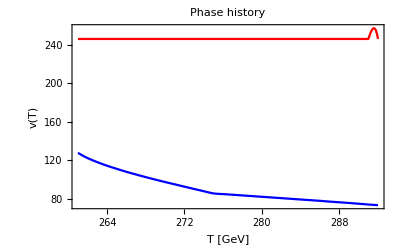

```mathematica
plot
```

```mathematica
Manipulate[Plot[V0[h]+VfiniteT[h,Temp],{h,0,f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{v},{}},PlotRange->All],{Temp,500,0}]
```

Plot::plln: Limiting value f in {h,0,f} is not a machine-sized real number.

# Stereographic parametrization

```mathematica
ClearAll["G_lobal`*"]
```

```mathematica
Npi=4;
pivec=Table[pi[i],{i,1,Npi}];
Pinorm=√(pivec.pivec);gmetric=f Table[KroneckerDelta[a,b]/(1+Pinorm^2/4)^2,{a,1,Npi},{b,Npi}];gmetricinverse=1/f Table[KroneckerDelta[a,b](1+Pinorm^2/4)^2,{a,1,Npi},{b,Npi}];
Print["Check g times g^-1"]
Print[MatrixForm[FullSimplify[gmetric.gmetricinverse]]];
dgilk=Hold[Sum[gmetricinverse[[i,m]](D[gmetric[[l,m]],pi[k]]+D[gmetric[[k,m]],pi[l]]-D[gmetric[[l,k]],pi[m]]),{m,1,Npi}]];Christoffel=1/2Table[ReleaseHold[dgilk],{i,1,Npi},{l,1,Npi},{k,1,Npi}];
Potential=G[Pinorm];
gD2V=Hold[Sum[gmetricinverse[[i,k]]D[Potential,pi[k],pi[j]],{k,1,Npi}]];
gGamDV=Hold[Sum[gmetricinverse[[i,l]] Christoffel[[m,j,l]]D[Potential,pi[m]],{m,1,Npi},{l,1,Npi}]];MassMatrix=Table[ReleaseHold[gD2V-gGamDV],{i,1,Npi},{j,1,Npi}];
```

Check g times g^-1

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
Integrate[1/(1+Pinorm^2/4),pi[2]]
```

(4 ArcTan[pi[2]/(√(4+pi[1]^2+pi[3]^2+pi[4]^2))])/(√(4+pi[1]^2+pi[3]^2+pi[4]^2))

```mathematica
Replace[ Simplify[Tr[MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(Sum[pi[i]^2,{i,1,Npi}])->Π^2,(4+Sum[pi[i]^2,{i,1,Npi}])->4+Π^2,(-12+Sum[pi[i]^2,{i,1,Npi}])->-12+Π^2},All]
```

-((4+Π^2) ((-12+Π^2) G'[√(Π^2)]-√(Π^2) (4+Π^2) G''[√(Π^2)]))/(16 f √(Π^2))

```mathematica
pivecST=Table[Dpi[i],{i,1,Npi}];
index=1;
EOMindex=Sum[Christoffel[[index,j,k]]pivecST[[j]]pivecST[[k]] ,{j,1,Npi},{k,1,Npi}]-Sum[D[Potential,pi[j]]gmetricinverse[[index,j]],{j,1,Npi}];FullSimplify[Replace[EOMindex/.Join[Table[pi[i]->0,{i,2,Npi}],Table[Dpi[i]->0,{i,2,Npi}]],{pi[1]->Π,Dpi[1]->Π'},All],Π>0]
```

-(2 Π (Π')^2)/(4+Π^2)-((4+Π^2)^2 G'[Π])/(16 f)

```mathematica
EOMpotentialTerm=FullSimplify[Sum[D[Potential,pi[i]]gmetricinverse[[i,j]] pi[j],{i,1,Npi},{j,1,Npi}]];Replace[EOMpotentialTerm,{√Sum[pi[i]^2,{i,1,Npi}]->Π,(4+Sum[pi[i]^2,{i,1,Npi}])->4+Π^2,Sum[pi[i] pi[i],{i,1,Npi}]->Π^2},All]
```

1/16 √(Π^2) (4+Π^2)^2 G'[√(Π^2)]

```mathematica
Simplify[Det[gmetricinverse]]
```

(1+1/4 (pi[1]^2+pi[2]^2+pi[3]^2))^6

```mathematica
pivecST=Table[Dpi[i],{i,1,Npi}];Simplify[Sum[Christoffel[[i,j,k]]pivecST[[j]]pivecST[[k]]pivec[[i]],{i,1,Npi},{j,1,Npi},{k,1,Npi}]]
```

1/(4+pi[1]^2+pi[2]^2+pi[3]^2)2 (-4 Dpi[2] Dpi[3] pi[2] pi[3]-4 Dpi[1] pi[1] (Dpi[2] pi[2]+Dpi[3] pi[3])+Dpi[3]^2 (pi[1]^2+pi[2]^2-pi[3]^2)+Dpi[2]^2 (pi[1]^2-pi[2]^2+pi[3]^2)+Dpi[1]^2 (-pi[1]^2+pi[2]^2+pi[3]^2))

```mathematica
dFpi=Table[D[1/(1+Pinorm^2/4),pi[i]],{i,1,Npi}];
```

```mathematica
FullSimplify[(1+Pinorm^2/4) Sum[dFpi.pivecST pivecST[[i]]pivec[[i]] ,{i,1,Npi}]]
```

-(2 (Dpi[1] pi[1]+Dpi[2] pi[2]+Dpi[3] pi[3])^2)/(4+pi[1]^2+pi[2]^2+pi[3]^2)

```mathematica
RadiativeStabilityEquation[Npi_]:=Module[{},
pivec=Table[pi[i],{i,1,Npi}];
Pinorm=√(pivec.pivec);gmetric=Table[KroneckerDelta[a,b]/(1+Pinorm^2/4)^2,{a,1,Npi},{b,Npi}];gmetricinverse=Table[KroneckerDelta[a,b](1+Pinorm^2/4)^2,{a,1,Npi},{b,Npi}];
(*Print["Check g times g^-1"];
Print[MatrixForm[FullSimplify[gmetric.gmetricinverse]]];*)
dgilk=Hold[Sum[gmetricinverse[[i,m]](D[gmetric[[l,m]],pi[k]]+D[gmetric[[k,m]],pi[l]]-D[gmetric[[l,k]],pi[m]]),{m,1,Npi}]];Christoffel=1/2Table[ReleaseHold[dgilk],{i,1,Npi},{l,1,Npi},{k,1,Npi}];
Potential=G[Pinorm];
gD2V=Hold[Sum[gmetricinverse[[i,k]]D[Potential,pi[k],pi[j]],{k,1,Npi}]];
gGamDV=Hold[Sum[gmetricinverse[[i,l]] Christoffel[[m,j,l]]D[Potential,pi[m]],{m,1,Npi},{l,1,Npi}]];MassMatrix=Table[ReleaseHold[gD2V-gGamDV],{i,1,Npi},{j,1,Npi}];
output=Replace[ Simplify[Tr[MassMatrix]],{√Sum[pi[i]^2,{i,1,Npi}]->Π,(Sum[pi[i]^2,{i,1,Npi}])->Π^2,(4+Sum[pi[i]^2,{i,1,Npi}])->4+Π^2,(-12+Sum[pi[i]^2,{i,1,Npi}])->-12+Π^2,√(Π^2)->Π},All];
Return[output]]
```

```mathematica
RadiativeStabilityEquation[2]
```

((4+Π^2)^2 (G'[Π]+Π G''[Π]))/(16 √(Π^2))

```mathematica
RadiativeStabilityEquation[3]
```

((4+Π^2) (8 G'[Π]+Π (4+Π^2) G''[Π]))/(16 √(Π^2))

```mathematica
RadiativeStabilityEquation[4]
```

-((4+Π^2) ((-12+Π^2) G'[Π]-Π (4+Π^2) G''[Π]))/(16 √(Π^2))

```mathematica
StereoSol[cc_,c1_,c2_]:=Module[{},sol4=DifferentialRoot[Function[{G,Π},{-((4+Π^2) ((-12+Π^2) G'[Π]-Π (4+Π^2) G''[Π]))/(16 Π)==cc G[Π],G[1]==c1,G'[1]==c2}]];
Return[sol4]
]
```

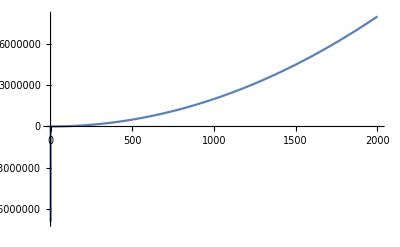

```mathematica
somesol=StereoSol[0,1,100];
Plot[somesol[p],{p,0,2000}]
```

```mathematica
Manipulate[somesol=StereoSol[c,c1,c2];Plot[somesol[p],{p,0,200}],{c,0,1000},{c1,-100,100},{c2,-100,100}]
```

DifferentialRoot::icond: Initial conditions should be of the form y[a] == b0, y'[a] == b1, ...

```mathematica
sol4=DSolve[{-((4+Π^2) ((-12+Π^2) G'[Π]-Π (4+Π^2) G''[Π]))/(16 Π)==-4G[Π]},G[Π],Π];Print[sol4]
```

{{G[Π]→(1-8/(4+Π^2)) C[1]+(C[2] (64-272 Π^2-4 Π^4+Π^6-192 Π^2 Log[Π]+48 Π^4 Log[Π]))/(2 Π^2 (4+Π^2))}}

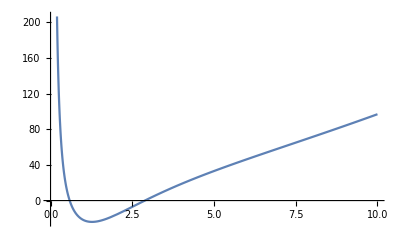

```mathematica
Plot[G[Π]/.sol4[[1]]/.{C[1]->1,C[2]->1},{Π,0,10}]
```

```mathematica
pp=1+p^2/4;pm=1-p^2/4;
FullSimplify[p^4/4-p^2/2 pp+p^2/4pm^2-1/2 pm^2 pp-p^2/2 pp+pp^2 -pp pm^2/2]
```

0

# Spherical vs Cartesian

```mathematica
ClearAll["Global`*"]
```

```mathematica
sol=DSolve[{G''[x]+2λ Cot[x]G'[x]+n(n+2λ)G[x]==0},G[x],x]
```

{{G[x]→C[1] (-1+Cos[x]^2)^(1/4 (1-2 λ)) LegendreP[1/2 (-1+2 n+2 λ),1/2 (-1+2 λ),Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4 (1-2 λ)) LegendreQ[1/2 (-1+2 n+2 λ),1/2 (-1+2 λ),Cos[x]]}}

```mathematica
GegebauerPotential[Ngb_,n_,z_]:=Module[{λ=(Ngb-1)/2},
sol=DSolve[{G''[x]+2λ Cot[x]G'[x]+n(n+2λ)G[x]==0},G[x],x];
Output=(G[x]/.(sol[[1]]/.{C[2]->0,C[1]->1}))/.{x->z};
Return[Output]
(*sol=NDSolve[{G''[x]+2λ Cot[x]G'[x]+n(n+2λ)G[x]==0,G'[x0]==0,G''[x0]==125.^2},G,{x,0,1}];
Return[ (G/.sol[[1]])[z]]*)
(*Output=(-1+Cos[z]^2)^(1/4 (1-2 λ)) LegendreP[1/2 (-1+2 n+2 λ),1/2 (-1+2 λ),Cos[z]];
Print[{1/2 (-1+2 n+2 λ),1/2 (-1+2 λ)}];
Return[Output]*)]
```

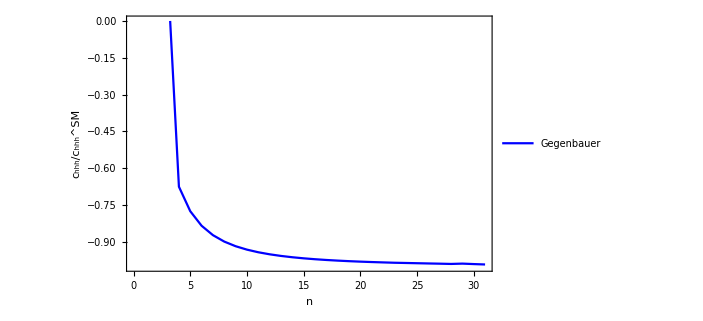

```mathematica
TrilinearHiggs[Ngb_,n_]:=Module[{mh=125,
v=246},
chhhSM=3 mh^2/v;
xmin=x/.NMinimize[{GegebauerPotential[Ngb,n,x],x>0,x<1},x][[2]];
f=v/xmin;
constant=mh^2/D[GegebauerPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->v};chhh=constant D[GegebauerPotential[Ngb,n,ϕ/f],{ϕ,3}]/.{ϕ->v};
Return[chhh/chhhSM]];
TrilinearCouplingsList=Table[{i,TrilinearHiggs[4,i]},{i,2,31,1}];plotInSpherical=ListPlot[TrilinearCouplingsList,PlotRange->{-1,0},Frame->True,FrameLabel->{"n","c_hhh/c_hhh^SM"},Joined->True,PlotStyle->{Blue},PlotLegends->Placed[{"Gegenbauer"},{.7,.7}]]
```

```mathematica
(*sdewffffffffff*)
```

```mathematica
GBPotential[Ngb_?NumberQ,x_?NumberQ,z_]:=Module[{},Return[Hypergeometric2F1[1/4 (-1+Ngb-2 x),1/4 (-1+Ngb+2 x),Ngb/2,z^2]]
];
TrilinearHiggs[Ngb_,n_]:=Module[{mh=125,
v=246},
chhhSM=3 mh^2/v;
xmin=x/.NMinimize[{GBPotential[Ngb,n,x],x>0,x<1},x][[2]];
f=v/xmin;
constant=mh^2/(D[GBPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->v});
chhh=constant Re[D[GBPotential[Ngb,n,ϕ/f],{ϕ,3}]/.{ϕ->v}];
Return[chhh/chhhSM]];
TrilinearCouplingsList=Table[{i,TrilinearHiggs[4,i]},{i,2,31,1}];
```

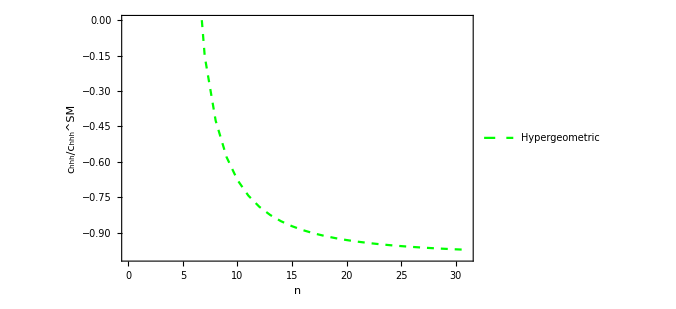

```mathematica
plotInSquareRoot=ListPlot[TrilinearCouplingsList,PlotRange->{-1,0},Joined->True,FrameLabel->{"n","c_hhh/c_hhh^SM"},PlotStyle->{Green,Dashed},PlotLegends->Placed[{"Hypergeometric"},{.7,.7}]]
```

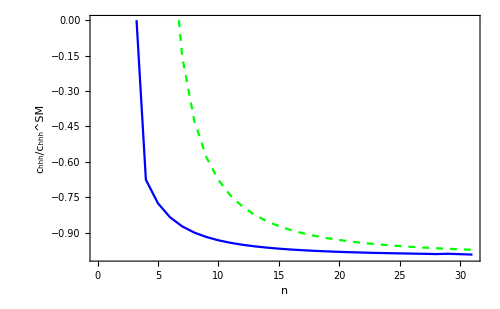

```mathematica
output=Show[plotInSpherical,plotInSquareRoot]
```

```mathematica
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/HiggsCoupling.pdf",output]
```

/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/HiggsCoupling.pdf

# Thermodynamics Hypergeometric

```mathematica
ClearAll["Global`*"];
JBData=Import["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/JB_spline.dat","Table"];
JBinterpolated=Interpolation[JBData];
Jmin=NMinimize[JBinterpolated[m2],{m2}];JBspline[m2_]:=If[m2>-3.7224781307403183,JBinterpolated[m2],Jmin[[1]]];
GBPotential[Ngb_?NumberQ,x_?NumberQ,z_]:=Module[{λ=(Ngb-1)/2},Return[Hypergeometric2F1[-x/2,x/2+λ,λ+1/2,z^2]](*Return[Hypergeometric2F1[-x,x+λ,λ+1/2,z^2]]*)(*Return[Hypergeometric2F1[1/4 (-1+Ngb-2 x),1/4 (-1+Ngb+2 x),Ngb/2,z^2]]*)
];
TrilinearHiggs[Ngb_,n_]:=Module[{mh=125,v=246},chhhSM=3 mh^2/v;
xmin1=x/.NMinimize[{GBPotential[Ngb,n,x],x>0,x<1},x][[2]];
xmin2=x/.FindMinimum[{GBPotential[Ngb,n,x],x>0,x<1},{x,0.}][[2]];xmin=Min[xmin1,xmin2];
f=v/xmin;
constant=mh^2/(D[GBPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->v});
chhh=constant Re[D[GBPotential[Ngb,n,ϕ/f],{ϕ,3}]/.{ϕ->v}];
Return[chhh/chhhSM]];
```

```mathematica
findAllTransitions[n_]:=Module[{Ngb=4,v=246},
λ=(Ngb-1)/2;
Gconstant=-n^2-2 n λ;
Print["Ngb=",Ngb," n=",n];
Print["c_hhh/c_hhh^SM=",TrilinearHiggs[Ngb,n]];
Print["f=",f," GeV"];
V0[ϕ_]:=If[ϕ<=f,constant GBPotential[Ngb,n,ϕ/f],constant];
fieldDependentMasses[h_]:=Gconstant V0[h]/f^2;
VfiniteT[h_,T_]:=If[T==0,0,T^4/2/π^2JBspline[fieldDependentMasses[h]/T^2]];
Print["The GB mass is given by ",(D[constant GBPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->246})^.5, "GeV"];
plot1=Plot[fieldDependentMasses[h],{h,0,f},Frame->True,FrameLabel->{"Π","M(Π)^2"},PlotStyle->{Blue,Dashed},PlotLabel->"Field dependent mass",PlotRange->All];plot2=Plot[V0[ϕ],{ϕ,0,f},Frame->True,FrameLabel->{"Π","V_tree(Π)^2"},PlotStyle->{Blue,Dashed},PlotLabel->"Tree level potential",PlotRange->All];
Print[plot1];
Print[plot2];
findMinimaAtT[T_]:=Module[{},
AllMinimaAtT=Quiet[Table[FindMinimum[{V0[h]+VfiniteT[h,T]},{h,h0},Method->"PrincipalAxis",WorkingPrecision->30],{h0,1,300,70}]];AllMinimaAtT=DeleteDuplicates[Round[(h/.{Transpose[AllMinimaAtT][[2]]})[[1]],.1]];
(*Print["Found minima at h = ",AllMinimaAtT];*)
eliminate={};For[i=1,i<=Length[AllMinimaAtT],i++,If[(AllMinimaAtT[[i]]<=300&&AllMinimaAtT[[i]]>=0),,AppendTo[eliminate,i]]];
AllMinimaAtT=Delete[AllMinimaAtT,Transpose[{eliminate}]];
(*Print["Selecting only minima at h = ",AllMinimaAtT];*)
Return[ReverseSort[AllMinimaAtT]]];
allPhases={{},{}};
Do[minima=findMinimaAtT[T];For[i=1,i<=Length[minima],i++,If[i==1,AppendTo[allPhases[[1]],{T,minima[[i]]}],AppendTo[allPhases[[2]],{T,minima[[i]]}]]];,{T,200,400,1}];
For[i=1,i<Length[allPhases[[1]]],i++,Trestored=Transpose[allPhases[[1]]][[1]][[i]];If[Transpose[allPhases[[1]]][[2]][[i]]<10^(-4),Print["Temperature is restored at T=",Trestored," GeV"];Break[]]];
plot3=ListPlot[{allPhases[[1]],allPhases[[2]]},Frame->True,FrameLabel->{"T [GeV]","v(T)"},PlotStyle->{Red,Blue,Dashed},PlotLabel->StringJoin["Phase history" ],PlotRange->All,GridLines->{{Trestored,Transpose[allPhases[[2]]][[1]][[-1]],Transpose[allPhases[[2]]][[1]][[1]]},{}}];
Print[plot3];
ϕ0=Interpolation[allPhases[[1]]];
ϕ1=Interpolation[allPhases[[2]]];
plot4=Plot[{ϕ0[T],ϕ1[T]},{T,Transpose[allPhases[[2]]][[1]][[1]],Transpose[allPhases[[2]]][[1]][[-1]]},Frame->True,FrameLabel->{"T [GeV]","v(T)"},PlotStyle->{Red,Blue,Dashed},PlotLabel->StringJoin["Phase history" ],PlotRange->All];Print[plot4];
DV[T_]:=(V0[ϕ0[T]]+VfiniteT[ϕ0[T],T])-(V0[ϕ1[T]]+VfiniteT[ϕ1[T],T]);
Tcritical=T/.FindRoot[DV[T],{T,Transpose[allPhases[[2]]][[1]][[1]],Transpose[allPhases[[2]]][[1]][[-1]]}];
Print["Critical temperature is given by Tc = ",Tcritical," GeV"];
dT=Transpose[allPhases[[2]]][[1]][[-1]]-Transpose[allPhases[[2]]][[1]][[1]];
Print["Phases coexist for ΔT=",dT," GeV"];
Print["Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}"];
output={Ngb,n,f,chhh/chhhSM,Trestored,Tcritical,dT};
Return[output]];
```

Ngb=4 n=20

c_hhh/c_hhh^SM=-0.940532

f=1038.34 GeV

The GB mass is given by 125.GeV

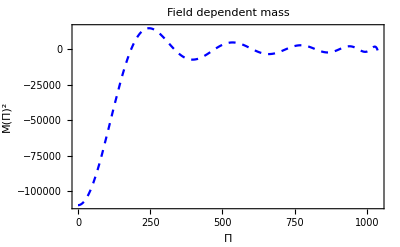

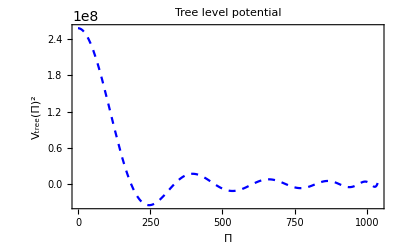

Temperature is restored at T=310 GeV

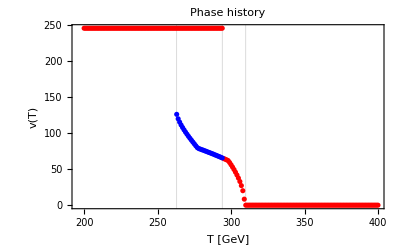

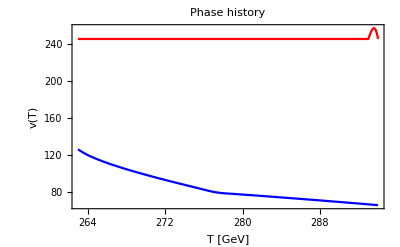

Critical temperature is given by Tc = 269.47 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

{4,20,1038.34,-0.940532,310,269.47,31}

```mathematica
Quiet[findAllTransitions[20]]
```

```mathematica
Manipulate[Plot[V0[f Cos[h]]+VfiniteT[f Cos[h],Temp],{h,-π/2,0},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->All],{Temp,f,0}]
```

Barrier Height measure is ΔV^(1/4)/T_c =0.17657

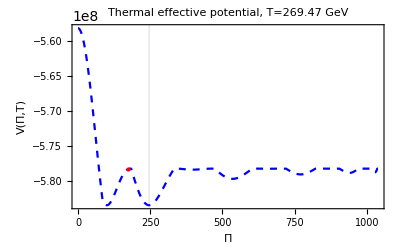

```mathematica
n=30.1;(Tcritical-√(24 f^2/(n (n+2λ))))/Tcritical;saddlePoint=Mean[{246,ϕ1[Tcritical]}];barrierHeight=Abs[Abs[((V0[h]+VfiniteT[h,Tcritical])/.{h->saddlePoint})]-Abs[((V0[246]+VfiniteT[246,Tcritical])/.{h->172})]]^(1/4)/Tcritical;
Print["Barrier Height measure is ΔV^(1/4)/T_c =",barrierHeight]
plot5=Plot[{V0[h]+VfiniteT[h,Tcritical]},{h,0,f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Tcritical]," GeV"],GridLines->{{246},{}},PlotRange->All,Epilog->{Red,PointSize@Large,Point[{saddlePoint,((V0[h]+VfiniteT[h,Tcritical])/.{h->saddlePoint})}]}];plot5
```

```mathematica
Temp=310;plot10=Plot[V0[h]+VfiniteT[h,Temp],{h,0,f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->All];
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/PLOTS/BPPotentialT1.pdf",plot10,"pdf"];
Temp=Tcritical+dT/2;
plot12=Plot[V0[h]+VfiniteT[h,Temp],{h,0,f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->All];
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/PLOTS/BPPotentialT3.pdf",plot12,"pdf"];
Temp=Tcritical;
plot11=Plot[{V0[h]+VfiniteT[h,Tcritical]},{h,0,f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Tcritical]," GeV"],GridLines->{{246},{}},PlotRange->All,Epilog->{Red,PointSize@Large,Point[{saddlePoint,((V0[h]+VfiniteT[h,Tcritical])/.{h->saddlePoint})}]}];
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/PLOTS/BPPotentialT2.pdf",plot11,"pdf"];
Temp=Tcritical-dT/4;
plot13=Plot[V0[h]+VfiniteT[h,Temp],{h,0,f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->All];
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/PLOTS/BPPotentialT4.pdf",plot13,"pdf"];
```

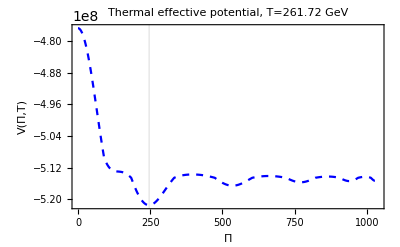

```mathematica
plot13
```

```mathematica
Manipulate[Plot[V0[h]+VfiniteT[h,Temp]+Temp^4π^2/90,{h,0,f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->{{-3 10^8,3 10^8}}],{Temp,f,0}]
```

```mathematica
Manipulate[Plot[V0[h]+VfiniteT[h,Temp],{h,0,f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->All],{Temp,f,0}]
```

Ngb=4 n=10

c_hhh/c_hhh^SM=-0.768159

f=567.045 GeV

The GB mass is given by 125.GeV

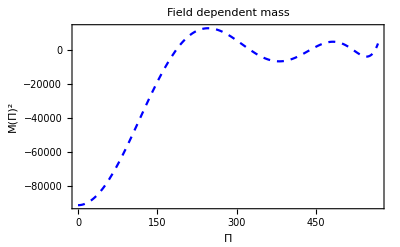

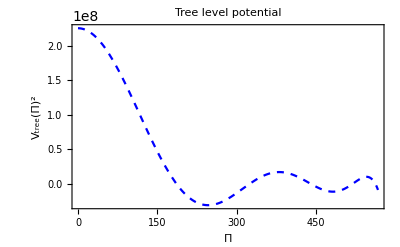

Temperature is restored at T=302 GeV

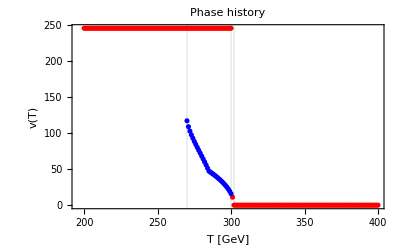

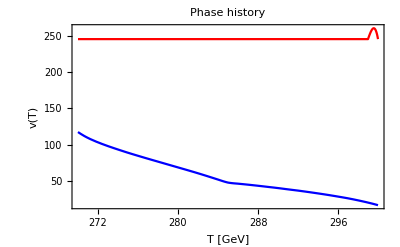

Critical temperature is given by Tc = 275.93 GeV

Phases coexist for ΔT=30 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=11

c_hhh/c_hhh^SM=-0.808473

f=613.581 GeV

The GB mass is given by 125.GeV

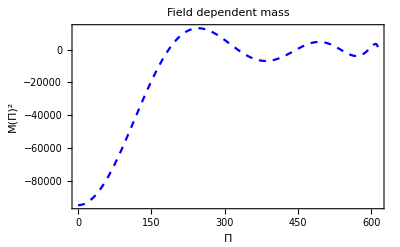

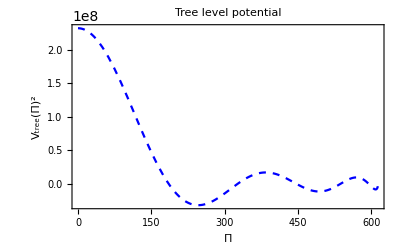

Temperature is restored at T=306 GeV

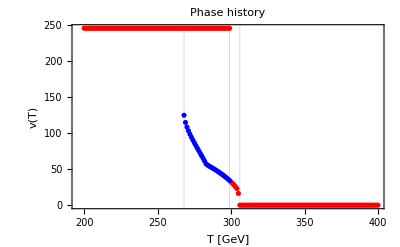

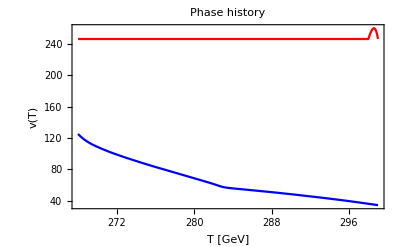

Critical temperature is given by Tc = 274.507 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=12

c_hhh/c_hhh^SM=-0.838849

f=660.333 GeV

The GB mass is given by 125.GeV

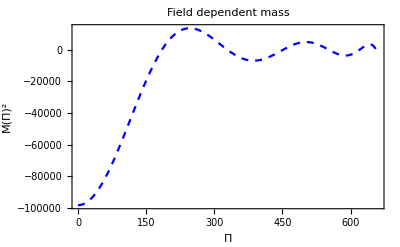

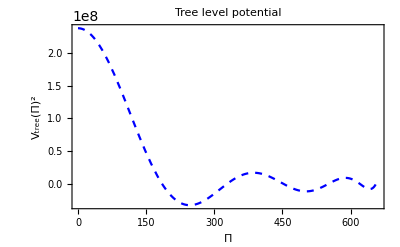

Temperature is restored at T=307 GeV

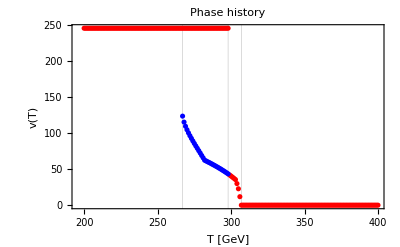

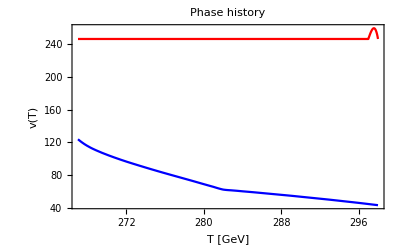

Critical temperature is given by Tc = 273.4 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=13

c_hhh/c_hhh^SM=-0.862367

f=707.254 GeV

The GB mass is given by 125.GeV

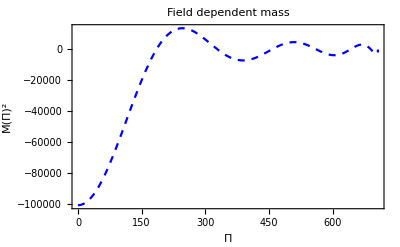

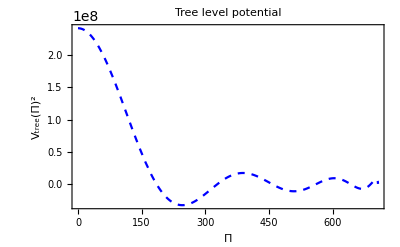

Temperature is restored at T=307 GeV

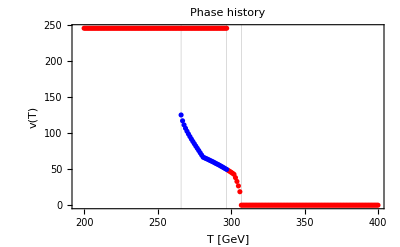

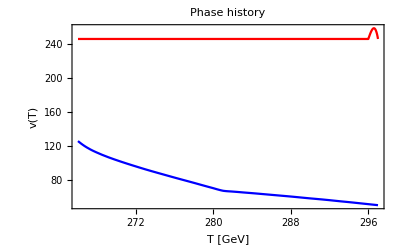

Critical temperature is given by Tc = 272.523 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=14

c_hhh/c_hhh^SM=-0.880982

f=754.307 GeV

The GB mass is given by 125.GeV

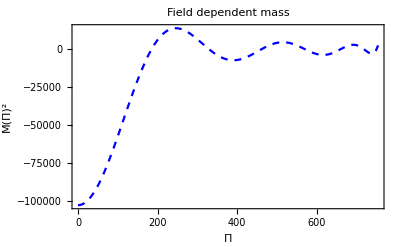

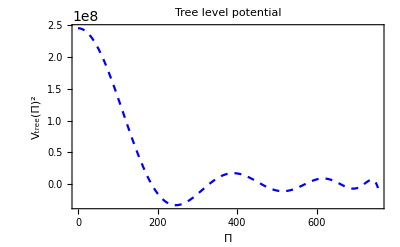

Temperature is restored at T=308 GeV

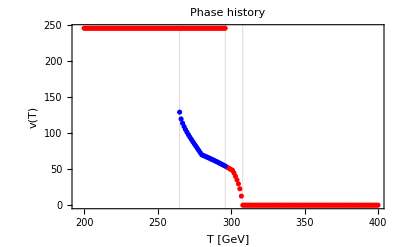

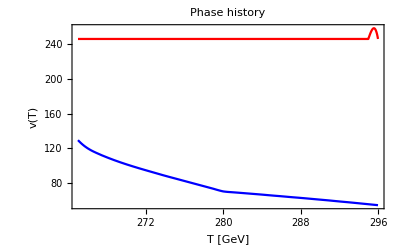

Critical temperature is given by Tc = 271.816 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=15

c_hhh/c_hhh^SM=-0.895991

f=801.468 GeV

The GB mass is given by 125.GeV

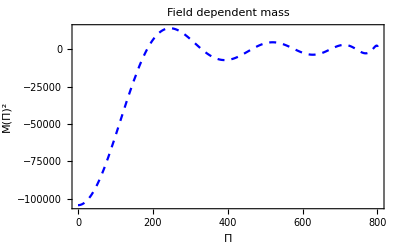

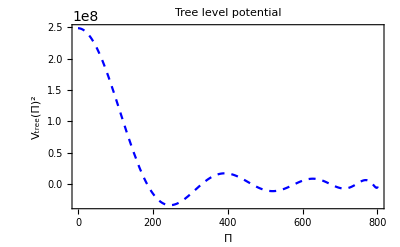

Temperature is restored at T=308 GeV

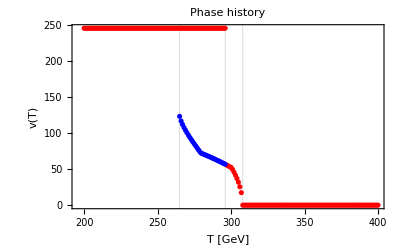

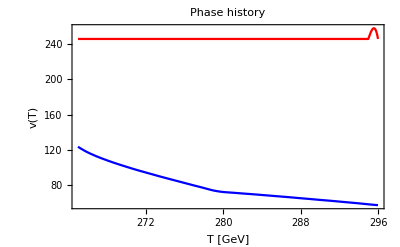

Critical temperature is given by Tc = 271.237 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=16

c_hhh/c_hhh^SM=-0.908282

f=848.717 GeV

The GB mass is given by 125.GeV

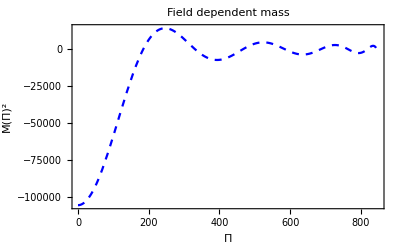

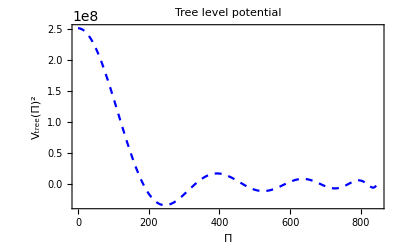

Temperature is restored at T=309 GeV

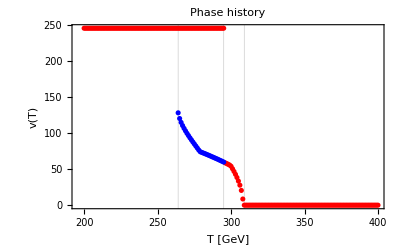

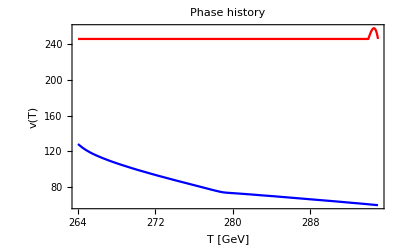

Critical temperature is given by Tc = 270.756 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=17

c_hhh/c_hhh^SM=-0.918483

f=896.04 GeV

The GB mass is given by 125.GeV

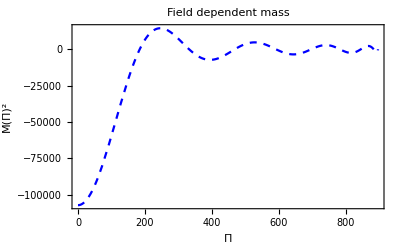

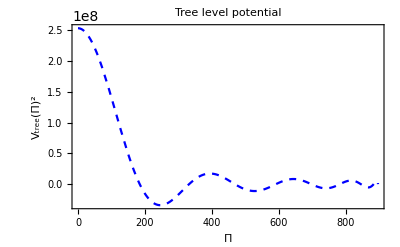

Temperature is restored at T=309 GeV

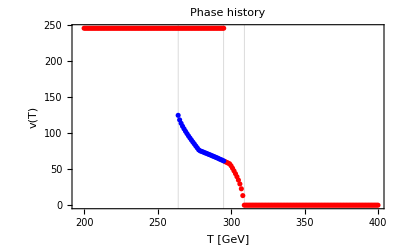

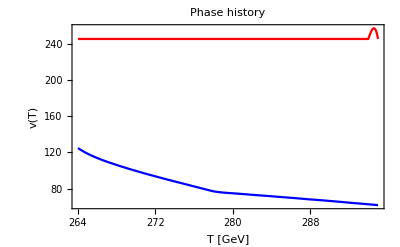

Critical temperature is given by Tc = 270.354 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=18

c_hhh/c_hhh^SM=-0.927048

f=943.423 GeV

The GB mass is given by 125.GeV

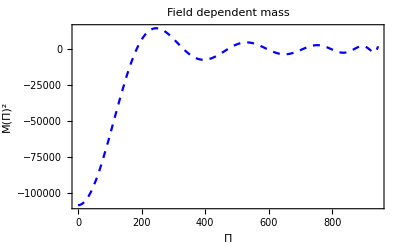

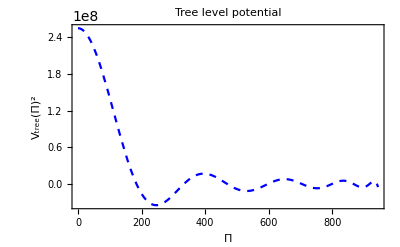

Temperature is restored at T=309 GeV

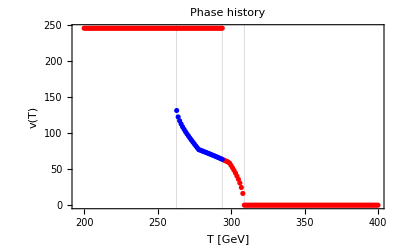

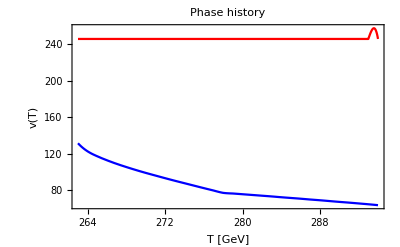

Critical temperature is given by Tc = 270.012 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=19

c_hhh/c_hhh^SM=-0.934313

f=990.858 GeV

The GB mass is given by 125.GeV

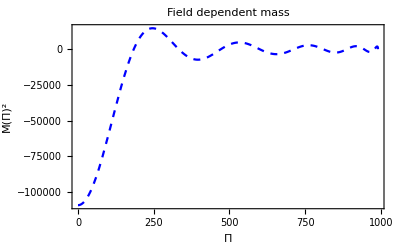

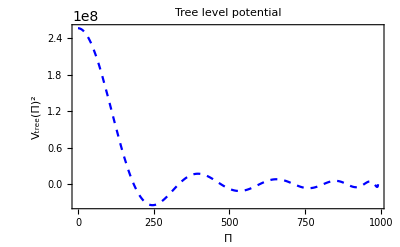

Temperature is restored at T=310 GeV

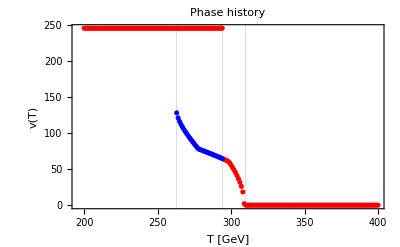

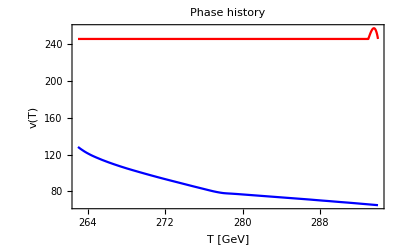

Critical temperature is given by Tc = 269.721 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=20

c_hhh/c_hhh^SM=-0.940532

f=1038.34 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=310 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 269.47 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=21

c_hhh/c_hhh^SM=-0.945899

f=1085.86 GeV

The GB mass is given by 125.GeV

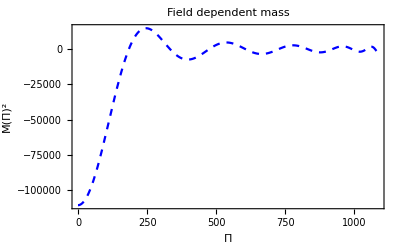

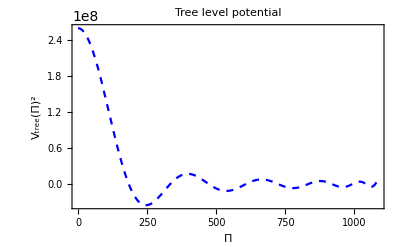

Temperature is restored at T=310 GeV

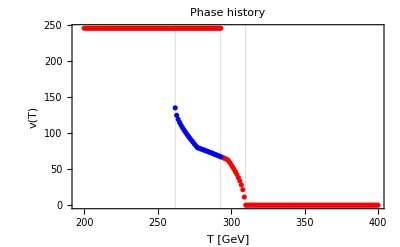

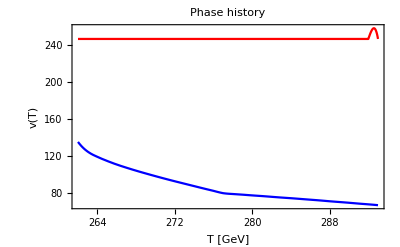

Critical temperature is given by Tc = 269.252 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=22

c_hhh/c_hhh^SM=-0.950563

f=1133.41 GeV

The GB mass is given by 125.GeV

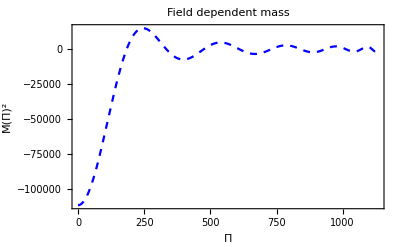

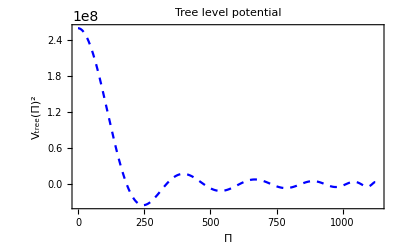

Temperature is restored at T=310 GeV

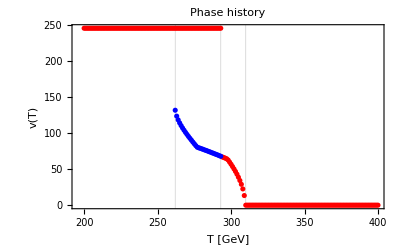

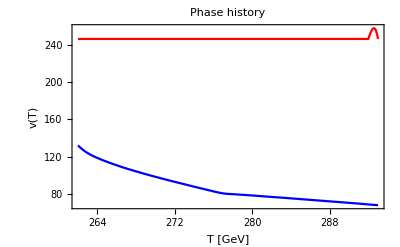

Critical temperature is given by Tc = 269.061 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=23

c_hhh/c_hhh^SM=-0.954643

f=1180.99 GeV

The GB mass is given by 125.GeV

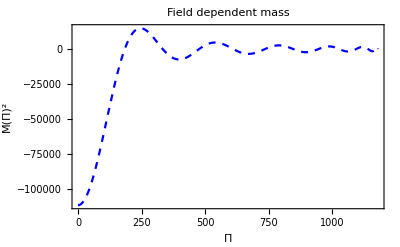

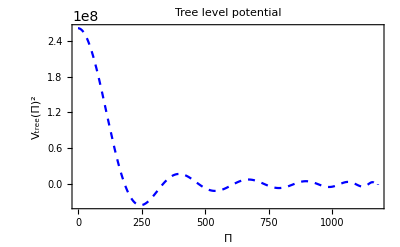

Temperature is restored at T=310 GeV

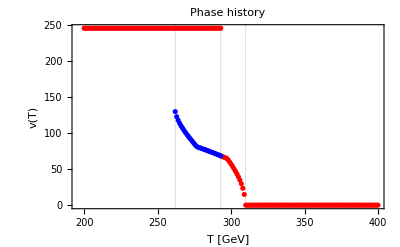

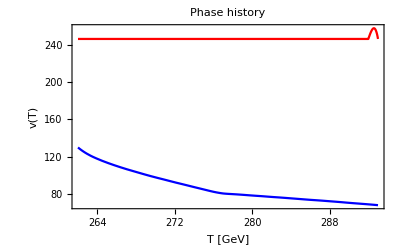

Critical temperature is given by Tc = 268.894 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=24

c_hhh/c_hhh^SM=-0.958234

f=1228.59 GeV

The GB mass is given by 125.GeV

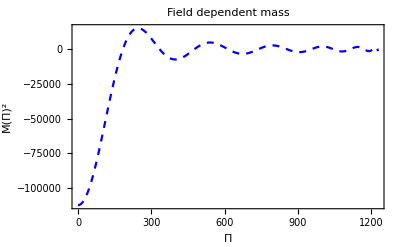

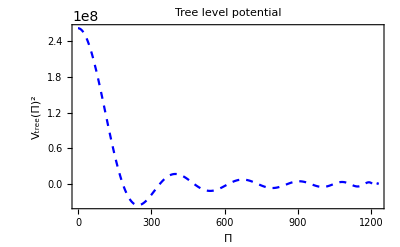

Temperature is restored at T=310 GeV

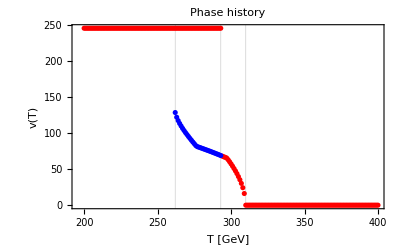

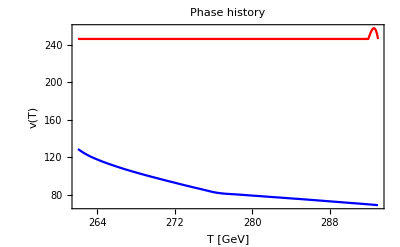

Critical temperature is given by Tc = 268.746 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=25

c_hhh/c_hhh^SM=-0.961411

f=1276.22 GeV

The GB mass is given by 125.GeV

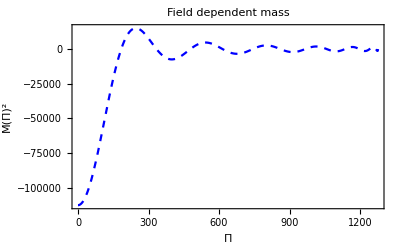

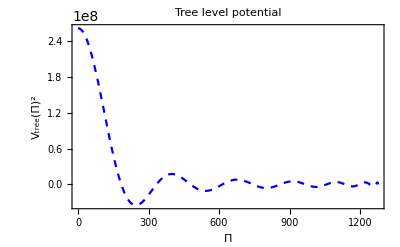

Temperature is restored at T=310 GeV

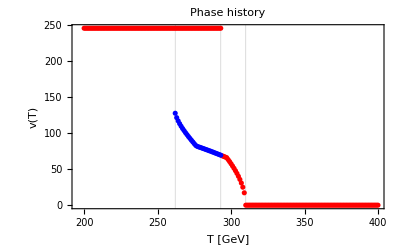

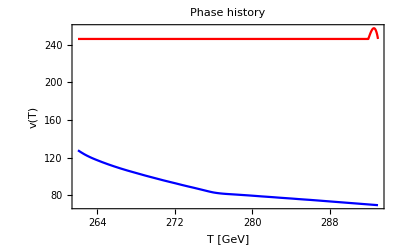

Critical temperature is given by Tc = 268.615 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=26

c_hhh/c_hhh^SM=-0.964237

f=1323.87 GeV

The GB mass is given by 125.GeV

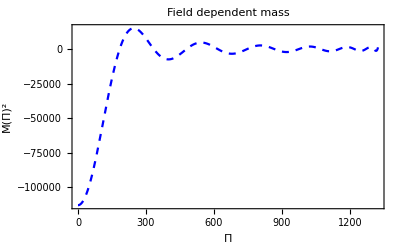

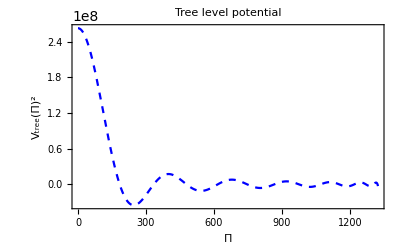

Temperature is restored at T=311 GeV

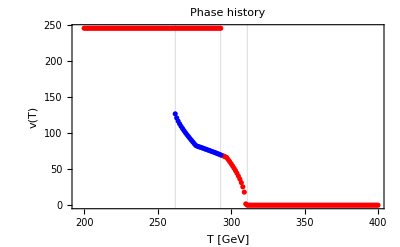

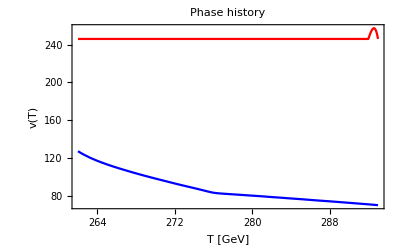

Critical temperature is given by Tc = 268.498 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=27

c_hhh/c_hhh^SM=-0.96676

f=1371.54 GeV

The GB mass is given by 125.GeV

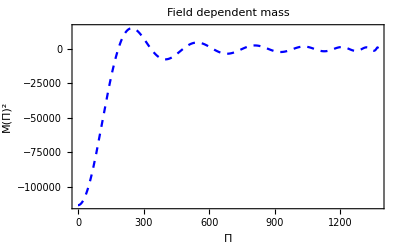

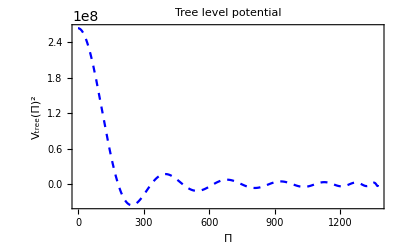

Temperature is restored at T=311 GeV

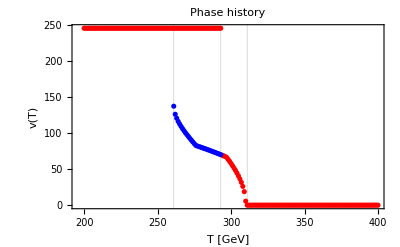

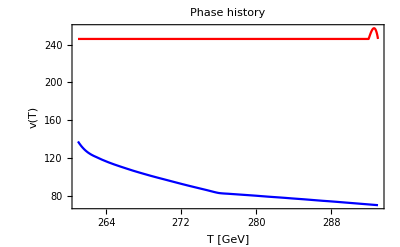

Critical temperature is given by Tc = 268.394 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=28

c_hhh/c_hhh^SM=-0.969025

f=1419.22 GeV

The GB mass is given by 125.GeV

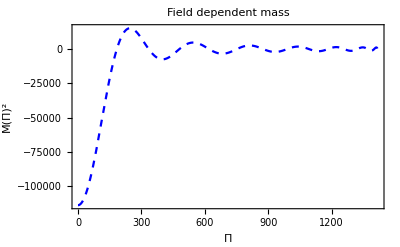

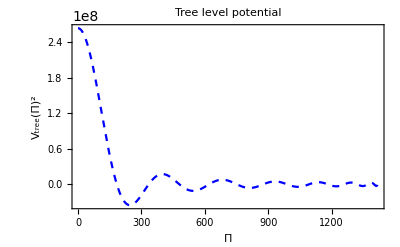

Temperature is restored at T=311 GeV

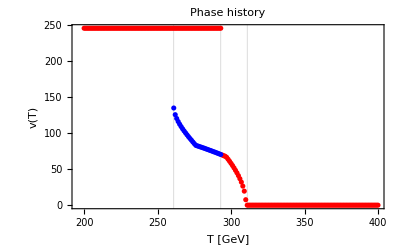

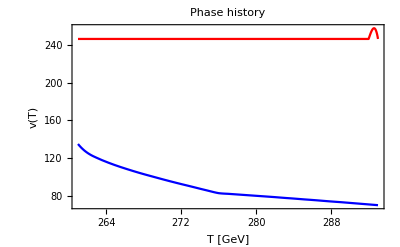

Critical temperature is given by Tc = 268.299 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=29

c_hhh/c_hhh^SM=-0.971063

f=1466.92 GeV

The GB mass is given by 125.GeV

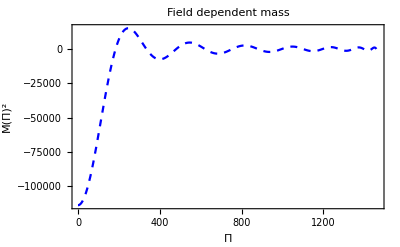

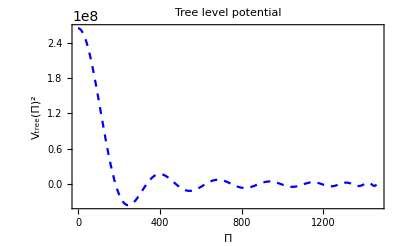

Temperature is restored at T=311 GeV

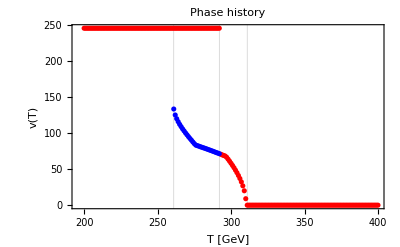

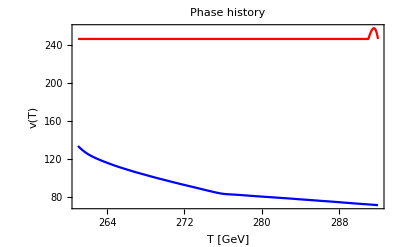

Critical temperature is given by Tc = 268.214 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=30

c_hhh/c_hhh^SM=-0.972906

f=1514.63 GeV

The GB mass is given by 125.GeV

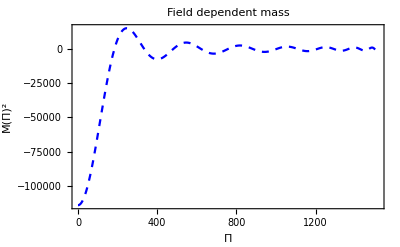

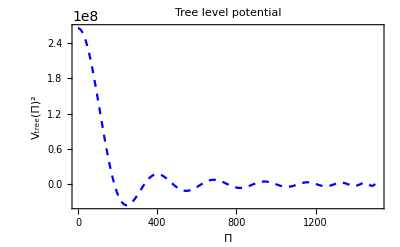

Temperature is restored at T=311 GeV

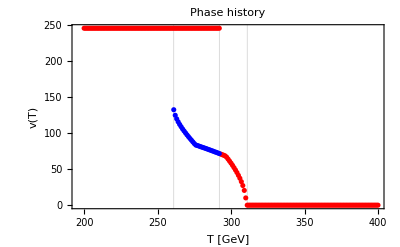

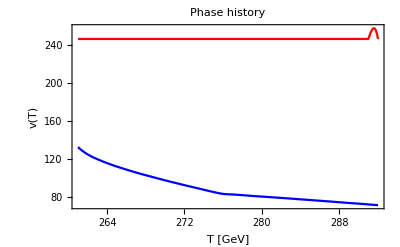

Critical temperature is given by Tc = 268.137 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=31

c_hhh/c_hhh^SM=-0.974578

f=1562.35 GeV

The GB mass is given by 125.GeV

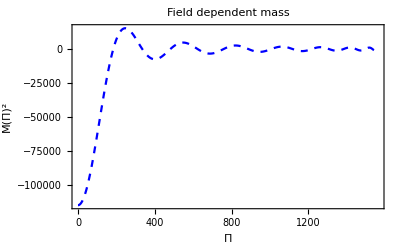

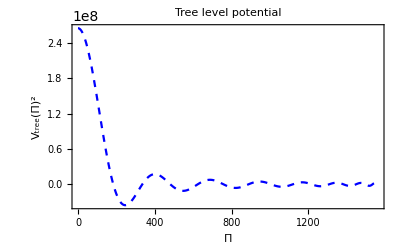

Temperature is restored at T=311 GeV

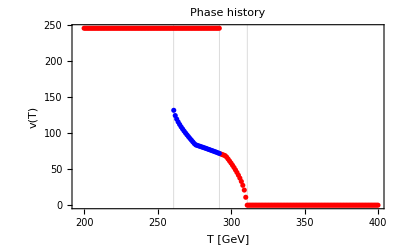

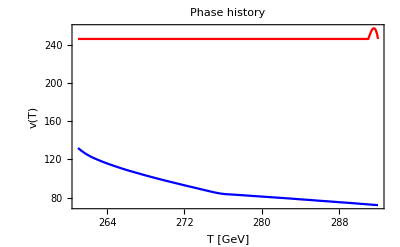

Critical temperature is given by Tc = 268.068 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=32

c_hhh/c_hhh^SM=-0.976098

f=1610.08 GeV

The GB mass is given by 125.GeV

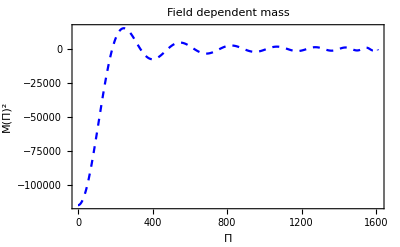

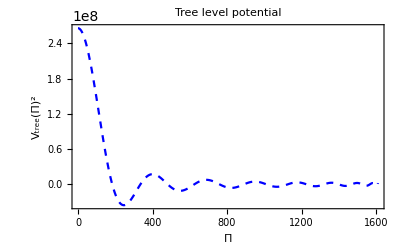

Temperature is restored at T=311 GeV

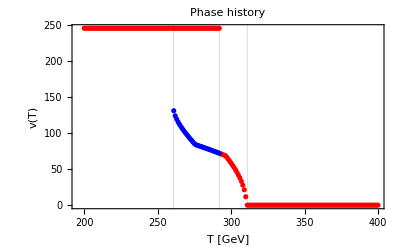

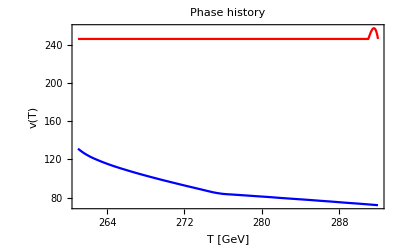

Critical temperature is given by Tc = 268.004 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=33

c_hhh/c_hhh^SM=-0.977486

f=1657.83 GeV

The GB mass is given by 125.GeV

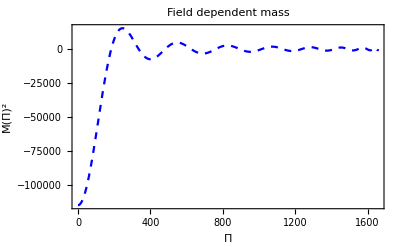

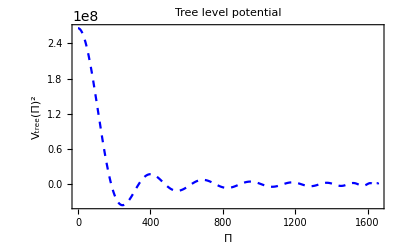

Temperature is restored at T=311 GeV

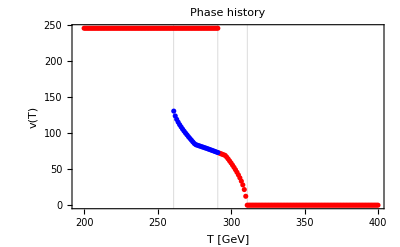

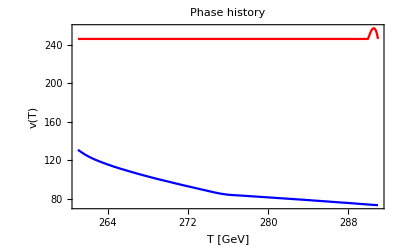

Critical temperature is given by Tc = 267.946 GeV

Phases coexist for ΔT=30 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=34

c_hhh/c_hhh^SM=-0.978755

f=1705.58 GeV

The GB mass is given by 125.GeV

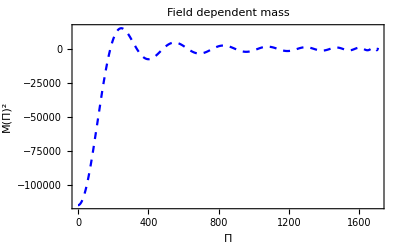

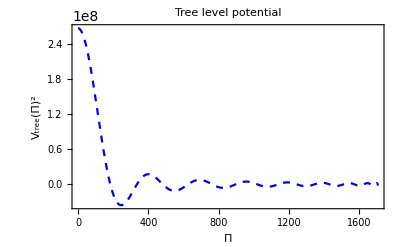

Temperature is restored at T=311 GeV

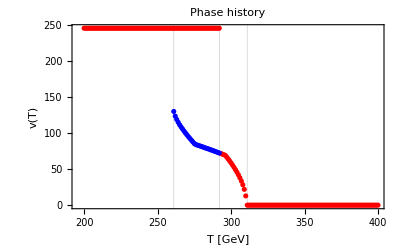

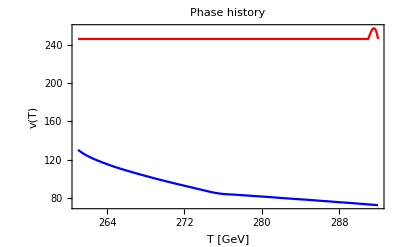

Critical temperature is given by Tc = 267.892 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=35

c_hhh/c_hhh^SM=-0.891281

f=785.58 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

Critical temperature is given by Tc = 191.697 GeV

Phases coexist for ΔT=200 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=36

c_hhh/c_hhh^SM=-0.980991

f=1801.11 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.798 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=37

c_hhh/c_hhh^SM=-0.981978

f=1848.88 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.757 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=38

c_hhh/c_hhh^SM=-0.98289

f=1896.66 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.718 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=39

c_hhh/c_hhh^SM=-0.983734

f=1944.45 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.682 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=40

c_hhh/c_hhh^SM=-0.984517

f=1992.24 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.649 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=41

c_hhh/c_hhh^SM=-0.985244

f=2040.04 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.619 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=42

c_hhh/c_hhh^SM=-0.985922

f=2087.84 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.59 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=43

c_hhh/c_hhh^SM=-0.986553

f=2135.65 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.563 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=44

c_hhh/c_hhh^SM=-0.987143

f=2183.46 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.538 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=45

c_hhh/c_hhh^SM=-0.987695

f=2231.27 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.515 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=46

c_hhh/c_hhh^SM=-0.842125

f=666.206 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

Critical temperature is given by Tc = T/.FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}] GeV

Phases coexist for ΔT=200 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Interpolation::inddp: The point 200. in dimension 1 is duplicated.

FindRoot::nlnum: The function value {-1.87561×10^8-8.10569×10^7 If[«1»]-1. If[Interpolation[{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«593»}][200.]≤666.206,constant GBPotential[Ngb$5023702,46.,Interpolation[«1»][«1»] Power[«2»]],constant]} is not a list of numbers with dimensions {1} at {T} = {200.}.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Interpolation::inddp: The point 200. in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

FindRoot::nlnum: The function value {-1.87561×10^8-8.10569×10^7 If[«1»]-1. If[Interpolation[{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«593»}][200.]≤666.206,constant GBPotential[Ngb$5023702,46.,Interpolation[«1»][«1»] Power[«2»]],constant]} is not a list of numbers with dimensions {1} at {T} = {200.}.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-1.87561×10^8-8.10569×10^7 If[«1»]-1. If[Interpolation[{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«593»}][200.]≤666.206,constant GBPotential[Ngb$5023702,46.,Interpolation[«1»][«1»] Power[«2»]],constant]} is not a list of numbers with dimensions {1} at {T} = {200.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
ThermoDynamics=Table[Quiet[findAllTransitions[n]],{n,10,46}];
```

```mathematica
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/HypergeometricData_new.csv",ThermoDynamics,"CSV"]
```

/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/HypergeometricData_new.csv

# Thermodynamics Hypergeometric_new

```mathematica
ClearAll["Global`*"];
JBData=Import["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/JB_spline.dat","Table"];
JBinterpolated=Interpolation[JBData];
Jmin=NMinimize[JBinterpolated[m2],{m2}];JBspline[m2_]:=If[m2>-3.7224781307403183,JBinterpolated[m2],Jmin[[1]]];
GBPotential[Ngb_?NumberQ,x_?NumberQ,z_]:=Module[{λ=(Ngb-1)/2},Return[Hypergeometric2F1[-x/2,x/2+λ,λ+1/2,z^2]](*Return[Hypergeometric2F1[-x,x+λ,λ+1/2,z^2]]*)(*Return[Hypergeometric2F1[1/4 (-1+Ngb-2 x),1/4 (-1+Ngb+2 x),Ngb/2,z^2]]*)
];
TrilinearHiggs[Ngb_,n_]:=Module[{mh=125,v=246},chhhSM=3 mh^2/v;
xmin1=x/.NMinimize[{GBPotential[Ngb,n,x],x>0,x<1},x][[2]];
xmin2=x/.FindMinimum[{GBPotential[Ngb,n,x],x>0,x<1},{x,0.}][[2]];xmin=Min[xmin1,xmin2];
f=v/xmin;
constant=mh^2/(D[GBPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->v});
chhh=constant Re[D[GBPotential[Ngb,n,ϕ/f],{ϕ,3}]/.{ϕ->v}];
Return[chhh/chhhSM]];
```

```mathematica
findAllTransitions[n_]:=Module[{Ngb=4,v=246},
λ=(Ngb-1)/2;
(*Gconstant=-n^2-2 n λ;*)
Print["Ngb=",Ngb," n=",n];
Print["c_hhh/c_hhh^SM=",TrilinearHiggs[Ngb,n]];
Print["f=",f," GeV"];
Λ=f;
V0[ϕ_]:=constant GBPotential[Ngb,n,ϕ/f];
Print["The GB mass is given by ",(D[constant GBPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->246})^.5, "GeV"];
plot1=Plot[V0[ϕ],{ϕ,0,f},Frame->True,FrameLabel->{"Π","V_tree(Π)"},PlotStyle->{Blue,Dashed},PlotLabel->"Tree level potential",PlotRange->All];
Print[plot1];fieldDependentMassHiggs[h_]:=((-h D[V0[ϕ],{ϕ,1}]/.{ϕ->h})+((f^2-h^2)D[V0[ϕ],{ϕ,2}]/.{ϕ->h}))/(f^2);
plot2=Plot[fieldDependentMassHiggs[h],{h,0,f},Frame->True,FrameLabel->{"Π","Mh(Π)^2"},PlotStyle->{Blue,Dashed},PlotLabel->"Field dependent mass",PlotRange->All];
Print[plot2];
fieldDependentMassGoldstone[h_]:=If[h<=.02,((f^2-h^2)D[V0[ϕ],{ϕ,1}]/.{ϕ->.2})/(f^2 (.2)),((f^2-h^2)D[V0[ϕ],{ϕ,1}]/.{ϕ->h})/(f^2 (h+10^-10))];
plot3=Plot[fieldDependentMassGoldstone[h],{h,0,f},Frame->True,FrameLabel->{"Π","MG(Π)^2"},PlotStyle->{Blue,Dashed},PlotLabel->"Field dependent mass",PlotRange->All];
Print[plot3];
VCW[h_]:=1/64/π^2( (Ngb-1)fieldDependentMassGoldstone[h]^2(Log[√(fieldDependentMassGoldstone[h]^2)/Λ^2]-1/2)+fieldDependentMassHiggs[h]^2(Log[√(fieldDependentMassHiggs[h]^2)/Λ^2]-1/2));
plot4=Plot[VCW[h],{h,0,f},Frame->True,FrameLabel->{"Π","V_CW(Π)"},PlotStyle->{Blue,Dashed},PlotLabel->"Coleman-Weinberg potential",PlotRange->All];
Print[plot4];
plot5=Plot[V0[h]+VCW[h],{h,0,f},Frame->True,FrameLabel->{"Π","V(Π)"},PlotStyle->{Blue,Dashed},PlotLabel->"Total potential at T=0",PlotRange->All];
Print[plot5];
VfiniteT[h_,T_]:=If[T==0,0,T^4/2/π^2(JBspline[fieldDependentMassHiggs[h]/T^2]+(Ngb-1)JBspline[fieldDependentMassGoldstone[h]/T^2])];
(*findMinimaAtT[T_]:=Module[{},
AllMinimaAtT=Quiet[Table[FindMinimum[{V0[h]+VCW[h]+VfiniteT[h,T]},{h,h0},Method->"PrincipalAxis",WorkingPrecision->30],{h0,1,300,70}]];AllMinimaAtT=DeleteDuplicates[Round[(h/.{Transpose[AllMinimaAtT][[2]]})[[1]],.1]];
(*Print["Found minima at h = ",AllMinimaAtT];*)
eliminate={};For[i=1,i<=Length[AllMinimaAtT],i++,If[(AllMinimaAtT[[i]]<=300&&AllMinimaAtT[[i]]>=0),,AppendTo[eliminate,i]]];
AllMinimaAtT=Delete[AllMinimaAtT,Transpose[{eliminate}]];
(*Print["Selecting only minima at h = ",AllMinimaAtT];*)
Return[ReverseSort[AllMinimaAtT]]];*)
findMinimaAtT[T_]:=Module[{},
AllMinimaAtT=Quiet[Table[Check[FindMinimum[{V0[h]+VCW[h]+VfiniteT[h,T]},{h,h0},Method->"PrincipalAxis",WorkingPrecision->30],,FindMinimum::nrnum],{h0,1,300,70}]];
AllMinimaAtT=DeleteCases[AllMinimaAtT,Null];
AllMinimaAtT=DeleteDuplicates[Round[(h/.{Transpose[AllMinimaAtT][[2]]})[[1]],.1]];
(*Print["Found minima at h = ",AllMinimaAtT];*)
eliminate={};For[i=1,i<=Length[AllMinimaAtT],i++,If[(AllMinimaAtT[[i]]<=300&&AllMinimaAtT[[i]]>=0),,AppendTo[eliminate,i]]];
AllMinimaAtT=Delete[AllMinimaAtT,Transpose[{eliminate}]];
(*Print["Selecting only minima at h = ",AllMinimaAtT];*)
Return[ReverseSort[AllMinimaAtT]]];
allPhases={{},{}};
Do[minima=findMinimaAtT[T];For[i=1,i<=Length[minima],i++,If[i==1,AppendTo[allPhases[[1]],{T,minima[[i]]}],AppendTo[allPhases[[2]],{T,minima[[i]]}]]];,{T,200,400,1}];
For[i=1,i<Length[allPhases[[1]]],i++,Trestored=Transpose[allPhases[[1]]][[1]][[i]];If[Transpose[allPhases[[1]]][[2]][[i]]<10^(-4),Print["Temperature is restored at T=",Trestored," GeV"];Break[]]];
plot6=ListPlot[{allPhases[[1]],allPhases[[2]]},Frame->True,FrameLabel->{"T [GeV]","v(T)"},PlotStyle->{Red,Blue,Dashed},PlotLabel->StringJoin["Phase history" ],PlotRange->All,GridLines->{{Trestored,Transpose[allPhases[[2]]][[1]][[-1]],Transpose[allPhases[[2]]][[1]][[1]]},{}}];
Print[plot6];
ϕ0=Interpolation[allPhases[[1]]];
ϕ1=Interpolation[allPhases[[2]]];
plot7=Plot[{ϕ0[T],ϕ1[T]},{T,Transpose[allPhases[[2]]][[1]][[1]],Transpose[allPhases[[2]]][[1]][[-1]]},Frame->True,FrameLabel->{"T [GeV]","v(T)"},PlotStyle->{Red,Blue,Dashed},PlotLabel->StringJoin["Phase history" ],PlotRange->All];Print[plot7];
DV[T_]:=((V0[ϕ0[T]]+VCW[ϕ0[T]]+VfiniteT[ϕ0[T],T])-(V0[ϕ1[T]]+VCW[ϕ1[T]]+VfiniteT[ϕ1[T],T]));
Tcritical=T/.FindRoot[DV[T],{T,Transpose[allPhases[[2]]][[1]][[1]],Transpose[allPhases[[2]]][[1]][[-1]]}];
Print["Critical temperature is given by Tc = ",Tcritical," GeV"];
dT=Transpose[allPhases[[2]]][[1]][[-1]]-Transpose[allPhases[[2]]][[1]][[1]];
Print["Phases coexist for ΔT=",dT," GeV"];
Print["Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}"];
output={Ngb,n,f,chhh/chhhSM,Trestored,Tcritical,dT};
Return[output]];
```

```mathematica
Quiet[findAllTransitions[20]]
```

Ngb=4 n=20

c_hhh/c_hhh^SM=-0.940532

f=1038.34 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=273 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 260.302 GeV

Phases coexist for ΔT=28 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

{4,20,1038.34,-0.940532,273,260.302,28}

```mathematica
Temp=253;
θmin=0;
θmax=.133π/2;
Gtot[h_]:=V0[f Sin[h]]+VCW[f Sin[h]]+VfiniteT[f Sin[h],Temp];
Gdata=Table[{h,Gtot[h]},{h,θmin,θmax,.008}];
Ginterpolated=Interpolation[Gdata];
Gfun[θ_]:=Ginterpolated[θ];Gfunprime[θ_]:=Evaluate[D[Gfun[θ],θ]];
```

```mathematica
rmin=0.01;rmax=100;θsol=NDSolve[{θ''[r]+2/r θ'[r]-Gfunprime[θ[r]]==0,θ'[rmin]==0,θ[rmin]==θmax-.1},θ,{r,rmin,rmax},MaxStepSize->0.001]
```

$Aborted

```mathematica
Plot[(θ/.θsol[[1]])[r],{r,rmin,rmax}]
```

-Graphics-

```mathematica
Manipulate[Plot[V0[h](1-n (n+2λ)Temp^2 4/24),{h,0,f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->All],{Temp,500,0}]
```

Plot::plln: Limiting value f in {h,0,f} is not a machine-sized real number.

```mathematica
Manipulate[Plot[-V0[f Sin[h]]-VCW[f Sin[h]]-VfiniteT[f Sin[h],Temp],{h,0,π/2},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->All],{Temp,500,0}]
```

```mathematica
Manipulate[Plot[V0[h]+VCW[h]+VfiniteT[h,Temp],{h,0,f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->All],{Temp,500,0}]
```

Plot::plln: Limiting value f in {h,0,f} is not a machine-sized real number.

```mathematica
ThermoDynamics=Table[Quiet[findAllTransitions[n]],{n,10,46}];
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/HypergeometricData_new.csv",ThermoDynamics,"CSV"]
```

Ngb=4 n=10

c_hhh/c_hhh^SM=-0.768159

f=567.045 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=282 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 271.599 GeV

Phases coexist for ΔT=21 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=11

c_hhh/c_hhh^SM=-0.808473

f=613.581 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=280 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 269.401 GeV

Phases coexist for ΔT=22 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=12

c_hhh/c_hhh^SM=-0.838849

f=660.333 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=279 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.626 GeV

Phases coexist for ΔT=23 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=13

c_hhh/c_hhh^SM=-0.862367

f=707.254 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=277 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 266.16 GeV

Phases coexist for ΔT=23 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=14

c_hhh/c_hhh^SM=-0.880982

f=754.307 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=276 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 264.93 GeV

Phases coexist for ΔT=24 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=15

c_hhh/c_hhh^SM=-0.895991

f=801.468 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=276 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 392.619 GeV

Phases coexist for ΔT=145 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=16

c_hhh/c_hhh^SM=-0.908282

f=848.717 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=275 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 262.975 GeV

Phases coexist for ΔT=26 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=17

c_hhh/c_hhh^SM=-0.918483

f=896.04 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=274 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 262.183 GeV

Phases coexist for ΔT=26 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=18

c_hhh/c_hhh^SM=-0.927048

f=943.423 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=274 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 261.484 GeV

Phases coexist for ΔT=27 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=19

c_hhh/c_hhh^SM=-0.934313

f=990.858 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=274 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 260.861 GeV

Phases coexist for ΔT=28 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=20

c_hhh/c_hhh^SM=-0.940532

f=1038.34 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=273 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 260.302 GeV

Phases coexist for ΔT=28 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=21

c_hhh/c_hhh^SM=-0.945899

f=1085.86 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=273 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 259.797 GeV

Phases coexist for ΔT=29 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=22

c_hhh/c_hhh^SM=-0.950563

f=1133.41 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=273 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 353.045 GeV

Phases coexist for ΔT=113 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=23

c_hhh/c_hhh^SM=-0.954643

f=1180.99 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=272 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 258.915 GeV

Phases coexist for ΔT=29 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=24

c_hhh/c_hhh^SM=-0.958234

f=1228.59 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=272 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 258.528 GeV

Phases coexist for ΔT=30 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=25

c_hhh/c_hhh^SM=-0.961411

f=1276.22 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=272 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 352.047 GeV

Phases coexist for ΔT=114 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=26

c_hhh/c_hhh^SM=-0.964237

f=1323.87 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=272 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 257.836 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=27

c_hhh/c_hhh^SM=-0.96676

f=1371.54 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=272 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 257.525 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=28

c_hhh/c_hhh^SM=-0.969025

f=1419.22 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=272 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 351.047 GeV

Phases coexist for ΔT=115 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=29

c_hhh/c_hhh^SM=-0.971063

f=1466.92 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 256.962 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=30

c_hhh/c_hhh^SM=-0.972906

f=1514.63 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 256.704 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=31

c_hhh/c_hhh^SM=-0.974578

f=1562.35 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 256.461 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=32

c_hhh/c_hhh^SM=-0.976098

f=1610.08 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 350.049 GeV

Phases coexist for ΔT=116 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=33

c_hhh/c_hhh^SM=-0.977486

f=1657.83 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 256.013 GeV

Phases coexist for ΔT=33 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=34

c_hhh/c_hhh^SM=-0.978755

f=1705.58 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 255.805 GeV

Phases coexist for ΔT=34 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=35

c_hhh/c_hhh^SM=-0.891281

f=785.58 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

Critical temperature is given by Tc = 114.217 GeV

Phases coexist for ΔT=200 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=36

c_hhh/c_hhh^SM=-0.980991

f=1801.11 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 349.049 GeV

Phases coexist for ΔT=116 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=37

c_hhh/c_hhh^SM=-0.981978

f=1848.88 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 255.236 GeV

Phases coexist for ΔT=35 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=38

c_hhh/c_hhh^SM=-0.98289

f=1896.66 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 255.062 GeV

Phases coexist for ΔT=35 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=39

c_hhh/c_hhh^SM=-0.983734

f=1944.45 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 254.895 GeV

Phases coexist for ΔT=34 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=40

c_hhh/c_hhh^SM=-0.984517

f=1992.24 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 254.734 GeV

Phases coexist for ΔT=35 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=41

c_hhh/c_hhh^SM=-0.985244

f=2040.04 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 348.05 GeV

Phases coexist for ΔT=117 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=42

c_hhh/c_hhh^SM=-0.985922

f=2087.84 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 254.43 GeV

Phases coexist for ΔT=35 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=43

c_hhh/c_hhh^SM=-0.986553

f=2135.65 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 254.286 GeV

Phases coexist for ΔT=36 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=44

c_hhh/c_hhh^SM=-0.987143

f=2183.46 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 254.147 GeV

Phases coexist for ΔT=36 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=45

c_hhh/c_hhh^SM=-0.987695

f=2231.27 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 254.012 GeV

Phases coexist for ΔT=36 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=46

c_hhh/c_hhh^SM=-0.842125

f=666.206 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

Critical temperature is given by Tc = T/.FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}] GeV

Phases coexist for ΔT=200 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Interpolation::inddp: The point 200. in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

FindRoot::nlnum: The function value {-7.1472×10^8-8.10569×10^7 (3. If[Times[«2»]>-«19»,«1»,Jmin⟦1⟧]+«1»)-«1»-0.00158314 (3. If[LessEqual[«2»],Times[«2»],Times[«2»]]^2 (-0.5+Log[Times[«2»]])+5.07651×10^-12 (-0.5+Log[Times[«2»]]) (Times[«3»]+Times[«3»])^2)} is not a list of numbers with dimensions {1} at {T} = {200.}.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-7.1472×10^8-8.10569×10^7 (3. If[Times[«2»]>-«19»,«1»,Jmin⟦1⟧]+«1»)-«1»-0.00158314 (3. If[LessEqual[«2»],Times[«2»],Times[«2»]]^2 (-0.5+Log[Times[«2»]])+5.07651×10^-12 (-0.5+Log[Times[«2»]]) (Times[«3»]+Times[«3»])^2)} is not a list of numbers with dimensions {1} at {T} = {200.}.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-7.1472×10^8-8.10569×10^7 (3. If[Times[«2»]>-«19»,«1»,Jmin⟦1⟧]+«1»)-«1»-0.00158314 (3. If[LessEqual[«2»],Times[«2»],Times[«2»]]^2 (-0.5+Log[Times[«2»]])+5.07651×10^-12 (-0.5+Log[Times[«2»]]) (Times[«3»]+Times[«3»])^2)} is not a list of numbers with dimensions {1} at {T} = {200.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Interpolation::inddp: The point 200. in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

FindRoot::nlnum: The function value {-7.1472×10^8-8.10569×10^7 (3. If[Times[«2»]>-«19»,«1»,Jmin⟦1⟧]+«1»)-«1»-0.00158314 (3. If[LessEqual[«2»],Times[«2»],Times[«2»]]^2 (-0.5+Log[Times[«2»]])+5.07651×10^-12 (-0.5+Log[Times[«2»]]) (Times[«3»]+Times[«3»])^2)} is not a list of numbers with dimensions {1} at {T} = {200.}.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-7.1472×10^8-8.10569×10^7 (3. If[Times[«2»]>-«19»,«1»,Jmin⟦1⟧]+«1»)-«1»-0.00158314 (3. If[LessEqual[«2»],Times[«2»],Times[«2»]]^2 (-0.5+Log[Times[«2»]])+5.07651×10^-12 (-0.5+Log[Times[«2»]]) (Times[«3»]+Times[«3»])^2)} is not a list of numbers with dimensions {1} at {T} = {200.}.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-7.1472×10^8-8.10569×10^7 (3. If[Times[«2»]>-«19»,«1»,Jmin⟦1⟧]+«1»)-«1»-0.00158314 (3. If[LessEqual[«2»],Times[«2»],Times[«2»]]^2 (-0.5+Log[Times[«2»]])+5.07651×10^-12 (-0.5+Log[Times[«2»]]) (Times[«3»]+Times[«3»])^2)} is not a list of numbers with dimensions {1} at {T} = {200.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/HypergeometricData_new.csv

# Thermodynamics Gegenbauer

```mathematica
ClearAll["Global`*"];
JBData=Import["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/JB_spline.dat","Table"];
JBinterpolated=Interpolation[JBData];
Jmin=NMinimize[JBinterpolated[m2],{m2}];JBspline[m2_]:=If[m2>-3.7224781307403183,JBinterpolated[m2],Jmin[[1]]];
```

```mathematica
Gfun[Ngb_,n_]:=Module[{fun,λ=(Ngb-1)/2,diffequation},
fun[x_]:=GegenbauerC[n,λ,Cos[x]];
Print["n+λ-1/2= ",n+λ-1/2];
Print[Plot[fun[x],{x,0,1},PlotRange->All]];
diffequation=D[fun[x],{x,2}]+2λ Cot[x]D[fun[x],x]+n(n+2λ)fun[x];
output=Table[(diffequation)/.{x->xx},{xx,0,1,.1}];
Print[FullSimplify[diffequation]];
Return[output]]
```

```mathematica
Gfun[4,20]
```

n+λ-1/2= 21

-Graphics-

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

0

{Indeterminate,1.20699×10^-6,-7.3202×10^-7,1.19768×10^-6,-8.8755×10^-7,1.10641×10^-6,2.96161×10^-7,-5.58794×10^-9,-1.21072×10^-8,1.86265×10^-9,3.25963×10^-9}

```mathematica
Clear[GBPotential];GBPotential[Ngb_?NumberQ,x_?NumberQ,z_]:=Module[{λ=(Ngb-1)/2},(*Return[Hypergeometric2F1[1/4 (-1+Ngb-2 x),1/4 (-1+Ngb+2 x),Ngb/2,z^2]]*)Return[GegenbauerC[x,λ,Cos[z]]]
];{legends,funcions}=Transpose[Table[{StringJoin["n=",ToString[i]],GBPotential[4,i,z]},{i,1,30,9}]];aplot=Plot[funcions,{z,0,π},(*AxesLabel->{"Π/F","G(Π/F)"},Axes->True*)Frame->True,FrameLabel->{"Π/F","G(Π/F)"},PlotLegends->legends,PlotRange->All]
```

-Graphics-

```mathematica
GBPotential[Ngb_?NumberQ,n_?NumberQ,z_]:=Module[{λ=(Ngb-1)/2},Return[GegenbauerC[n,λ,Cos[z]]]];
TrilinearHiggs[Ngb_,n_]:=Module[{mh=125,v=246},
chhhSM=3 mh^2/v;
xmin1=x/.NMinimize[{GBPotential[Ngb,n,x],x>0,x<1},x][[2]];
xmin2=x/.FindMinimum[{GBPotential[Ngb,n,x],x>0,x<1},{x,0.1}][[2]];xmin=Min[xmin1,xmin2];
f=v/xmin;
constant=mh^2/(D[GBPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->v});
chhh=constant Re[D[GBPotential[Ngb,n,ϕ/f],{ϕ,3}]/.{ϕ->v}];
Return[chhh/chhhSM]];
```

```mathematica
findAllTransitions[n_]:=Module[{Ngb=4,v=246},
λ=(Ngb-1)/2;
Print["Ngb=",Ngb," n=",n];
Print["c_hhh/c_hhh^SM=",TrilinearHiggs[Ngb,n]];
Print["f=",f," GeV"];
V0[ϕ_]:=constant GBPotential[Ngb,n,ϕ/f];
fieldDependentMasses[h_]:=(-n^2-2λ n)V0[h]/f^2;
VfiniteT[h_,T_]:=If[T==0,0,T^4/2/π^2JBspline[fieldDependentMasses[h]/T^2]];
Print["The GB mass is given by ",(D[constant GBPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->246})^.5, "GeV"];
plot1=Plot[fieldDependentMasses[h],{h,0,f},Frame->True,FrameLabel->{"Π","m(Π)^2"},PlotStyle->{Blue,Dashed},PlotLabel->"Field dependent mass",PlotRange->All];plot2=Plot[V0[ϕ],{ϕ,0,f},Frame->True,FrameLabel->{"Π","V_tree(Π)^2"},PlotStyle->{Blue,Dashed},PlotLabel->"Tree level potential",PlotRange->All];
Print[plot1];
Print[plot2];
findMinimaAtT[T_]:=Module[{},
AllMinimaAtT=Quiet[Table[FindMinimum[{V0[h]+VfiniteT[h,T]},{h,h0},Method->"PrincipalAxis",WorkingPrecision->30],{h0,1,300,70}]];AllMinimaAtT=DeleteDuplicates[Round[(h/.{Transpose[AllMinimaAtT][[2]]})[[1]],.1]];
(*Print["Found minima at h = ",AllMinimaAtT];*)
eliminate={};For[i=1,i<=Length[AllMinimaAtT],i++,If[(AllMinimaAtT[[i]]<=300&&AllMinimaAtT[[i]]>=0),,AppendTo[eliminate,i]]];
AllMinimaAtT=Delete[AllMinimaAtT,Transpose[{eliminate}]];
(*Print["Selecting only minima at h = ",AllMinimaAtT];*)
Return[ReverseSort[AllMinimaAtT]]];
allPhases={{},{}};
Do[minima=findMinimaAtT[T];For[i=1,i<=Length[minima],i++,If[i==1,AppendTo[allPhases[[1]],{T,minima[[i]]}],AppendTo[allPhases[[2]],{T,minima[[i]]}]]];,{T,200,400,1}];
For[i=1,i<Length[allPhases[[1]]],i++,Trestored=Transpose[allPhases[[1]]][[1]][[i]];If[Transpose[allPhases[[1]]][[2]][[i]]<10^(-4),Print["Temperature is restored at T=",Trestored," GeV"];Break[]]];
plot3=ListPlot[{allPhases[[1]],allPhases[[2]]},Frame->True,FrameLabel->{"T [GeV]","v(T)"},PlotStyle->{Red,Blue,Dashed},PlotLabel->StringJoin["Phase history" ],PlotRange->All,GridLines->{{Trestored,Transpose[allPhases[[2]]][[1]][[-1]],Transpose[allPhases[[2]]][[1]][[1]]},{}}];
Print[plot3];
ϕ0=Interpolation[allPhases[[1]]];
ϕ1=Interpolation[allPhases[[2]]];
plot4=Plot[{ϕ0[T],ϕ1[T]},{T,Transpose[allPhases[[2]]][[1]][[1]],Transpose[allPhases[[2]]][[1]][[-1]]},Frame->True,FrameLabel->{"T [GeV]","v(T)"},PlotStyle->{Red,Blue,Dashed},PlotLabel->StringJoin["Phase history" ],PlotRange->All];
Print[plot4];
DV[T_]:=(V0[ϕ0[T]]+VfiniteT[ϕ0[T],T])-(V0[ϕ1[T]]+VfiniteT[ϕ1[T],T]);
Tcritical=T/.FindRoot[DV[T],{T,Transpose[allPhases[[2]]][[1]][[1]],Transpose[allPhases[[2]]][[1]][[-1]]}];
Print["Critical temperature is given by Tc = ",Tcritical," GeV"];
dT=Transpose[allPhases[[2]]][[1]][[-1]]-Transpose[allPhases[[2]]][[1]][[1]];
Print["Phases coexist for ΔT=",dT," GeV"];
Print["Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}"];
output={Ngb,n,f,chhh/chhhSM,Trestored,Tcritical,dT};
Return[output]];
```

```mathematica
Quiet[findAllTransitions[20]]
```

Ngb=4 n=20

c_hhh/c_hhh^SM=-0.980856

f=1028.47 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.268 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

{4,20,1028.47,-0.980856,311,267.268,32}

```mathematica
n=40;(Tcritical-√(24 f^2/(n (n+2λ))))/Tcritical
```

0.121416

```mathematica
saddlePoint=Mean[{246,ϕ1[Tcritical]}];barrierHeight=Abs[Abs[((V0[h]+VfiniteT[h,Tcritical])/.{h->saddlePoint})]-Abs[((V0[246]+VfiniteT[246,Tcritical])/.{h->172})]]^(1/4)/Tcritical;
Print["Barrier Height measure is ΔV^(1/4)/T_c =",barrierHeight]
plot5=Plot[{V0[h]+VfiniteT[h,Tcritical]},{h,0,π f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->All,Epilog->{Red,PointSize@Large,Point[{saddlePoint,((V0[h]+VfiniteT[h,Tcritical])/.{h->saddlePoint})}]}];plot5
```

Barrier Height measure is ΔV^(1/4)/T_c =0.179543

-Graphics-

```mathematica
n=20;
```

```mathematica
Manipulate[Plot[V0[h]-Temp^2 n(n+2λ)V0[h]/f^2,{h,0,π f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->{-Temp^4,Temp^4}],{Temp,500,0}]
```

Plot::plln: Limiting value f π in {h,0,f π} is not a machine-sized real number.

```mathematica
Manipulate[Plot[V0[h]+VfiniteT[h,Temp],{h,0,π f},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->{-Temp^4,Temp^4}],{Temp,500,0}]
```

Plot::plln: Limiting value f π in {h,0,f π} is not a machine-sized real number.

```mathematica
ThermoDynamics=Table[Quiet[findAllTransitions[n]],{n,4,46}];
```

Ngb=4 n=4

c_hhh/c_hhh^SM=-0.675511

f=257.506 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=302 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 271.091 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=5

c_hhh/c_hhh^SM=-0.775376

f=306.455 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=305 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 269.966 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=6

c_hhh/c_hhh^SM=-0.83464

f=355.077 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=307 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 269.241 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=7

c_hhh/c_hhh^SM=-0.872924

f=403.507 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=308 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 268.75 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=8

c_hhh/c_hhh^SM=-0.899174

f=451.816 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=309 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 268.403 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=9

c_hhh/c_hhh^SM=-0.917993

f=500.04 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=309 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 268.149 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=10

c_hhh/c_hhh^SM=-0.93196

f=548.205 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=310 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.957 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=11

c_hhh/c_hhh^SM=-0.94262

f=596.325 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=310 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.809 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=12

c_hhh/c_hhh^SM=-0.950945

f=644.411 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=310 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.693 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=13

c_hhh/c_hhh^SM=-0.957574

f=692.471 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=310 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.6 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=14

c_hhh/c_hhh^SM=-0.96294

f=740.51 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.524 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=15

c_hhh/c_hhh^SM=-0.967345

f=788.531 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.461 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=16

c_hhh/c_hhh^SM=-0.971006

f=836.538 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.409 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=17

c_hhh/c_hhh^SM=-0.974084

f=884.533 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.365 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=18

c_hhh/c_hhh^SM=-0.976703

f=932.518 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.327 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=19

c_hhh/c_hhh^SM=-0.978927

f=980.496 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.296 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=20

c_hhh/c_hhh^SM=-0.980856

f=1028.47 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.268 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=21

c_hhh/c_hhh^SM=-0.982528

f=1076.43 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.244 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=22

c_hhh/c_hhh^SM=-0.983993

f=1124.39 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

Temperature is restored at T=311 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.223 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=23

c_hhh/c_hhh^SM=-0.985373

f=1172.33 GeV

The GB mass is given by 125.GeV

/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/gegenbauerData.csv

```mathematica
(*Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/gegenbauerData.csv",gegenbauerData,"CSV"]*)
gegenbauerData=Import["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/gegenbauerData.csv"];
```

```mathematica
Print["{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}"]
```

{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

```mathematica
ListPlot[Transpose[{gegenbauerData[[2]],gegenbauerData[[3]]}],PlotRange->All]
```

-Graphics-

# Thermodynamics Gegenbauer_new

```mathematica
ClearAll["Global`*"];
JBData=Import["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/JB_spline.dat","Table"];
JBinterpolated=Interpolation[JBData];
Jmin=NMinimize[JBinterpolated[m2],{m2}];JBspline[m2_]:=If[m2>-3.7224781307403183,JBinterpolated[m2],Jmin[[1]]];
GBPotential[Ngb_?NumberQ,n_?NumberQ,z_]:=Module[{λ=(Ngb-1)/2},Return[GegenbauerC[n,λ,Cos[z]]]];
TrilinearHiggs[Ngb_,n_]:=Module[{mh=125,v=246},
chhhSM=3 mh^2/v;
xmin1=x/.NMinimize[{GBPotential[Ngb,n,x],x>0,x<1},x][[2]];
xmin2=x/.FindMinimum[{GBPotential[Ngb,n,x],x>0,x<1},{x,0.1}][[2]];xmin=Min[xmin1,xmin2];
f=v/xmin;
constant=mh^2/(D[GBPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->v});
chhh=constant Re[D[GBPotential[Ngb,n,ϕ/f],{ϕ,3}]/.{ϕ->v}];
Return[chhh/chhhSM]];
```

```mathematica
findAllTransitions[n_]:=Module[{Ngb=4,v=246},
λ=(Ngb-1)/2;
(*Gconstant=-n^2-2 n λ;*)
Print["Ngb=",Ngb," n=",n];
Print["c_hhh/c_hhh^SM=",TrilinearHiggs[Ngb,n]];
Print["f=",f," GeV"];
Λ=π f/2;
V0[ϕ_]:=constant GBPotential[Ngb,n,ϕ/f];
Print["The GB mass is given by ",(D[constant GBPotential[Ngb,n,ϕ/f],{ϕ,2}]/.{ϕ->246})^.5, "GeV"];
plot1=Plot[V0[ϕ],{ϕ,0,Λ},Frame->True,FrameLabel->{"Π","V_tree(Π)"},PlotStyle->{Blue,Dashed},PlotLabel->"Tree level potential",PlotRange->All];
Print[plot1];
fieldDependentMassHiggs[h_]:=((-h D[V0[ϕ],{ϕ,1}]/.{ϕ->h})+((f^2-h^2)D[V0[ϕ],{ϕ,2}]/.{ϕ->h}))/(f^2);
plot2=Plot[fieldDependentMassHiggs[h],{h,0,Λ},Frame->True,FrameLabel->{"Π","Mh(Π)^2"},PlotStyle->{Blue,Dashed},PlotLabel->"Field dependent mass",PlotRange->All];
Print[plot2];
fieldDependentMassGoldstone[h_]:=If[h<=.02,((f^2-h^2)D[V0[ϕ],{ϕ,1}]/.{ϕ->.2})/(f^2 (.2)),((f^2-h^2)D[V0[ϕ],{ϕ,1}]/.{ϕ->h})/(f^2 (h+10^-10))];
plot3=Plot[fieldDependentMassGoldstone[h],{h,0,Λ},Frame->True,FrameLabel->{"Π","MG(Π)^2"},PlotStyle->{Blue,Dashed},PlotLabel->"Field dependent mass",PlotRange->All];
Print[plot3];
VCW[h_]:=1/64/π^2( (Ngb-1)fieldDependentMassGoldstone[h]^2(Log[√(fieldDependentMassGoldstone[h]^2)/Λ^2]-1/2)+fieldDependentMassHiggs[h]^2(Log[√(fieldDependentMassHiggs[h]^2)/Λ^2]-1/2));
plot4=Plot[VCW[h],{h,0,Λ},Frame->True,FrameLabel->{"Π","V_CW(Π)"},PlotStyle->{Blue,Dashed},PlotLabel->"Coleman-Weinberg potential",PlotRange->All];
Print[plot4];
plot5=Plot[V0[h]+VCW[h],{h,0,Λ},Frame->True,FrameLabel->{"Π","V(Π)"},PlotStyle->{Blue,Dashed},PlotLabel->"Total potential at T=0",PlotRange->All];
Print[plot5];
VfiniteT[h_,T_]:=If[T==0,0,T^4/2/π^2(JBspline[fieldDependentMassHiggs[h]/T^2]+(Ngb-1)JBspline[fieldDependentMassGoldstone[h]/T^2])];
(*findMinimaAtT[T_]:=Module[{},
AllMinimaAtT=Quiet[Table[Check[FindMinimum[{V0[h]+VCW[h]+VfiniteT[h,T]},{h,h0},Method->"PrincipalAxis",WorkingPrecision->30],,FindMinimum::nrnum],{h0,0,370,70}]];
AllMinimaAtT=DeleteCases[AllMinimaAtT,Null];
(*Print[Round[(h/.{Transpose[AllMinimaAtT][[2]]})[[1]],.1]];*)
AllMinimaAtT=DeleteDuplicates[Round[(h/.{Transpose[AllMinimaAtT][[2]]})[[1]],.2]];
eliminate={};For[i=1,i<=Length[AllMinimaAtT],i++,If[(AllMinimaAtT[[i]]<=300&&AllMinimaAtT[[i]]>=0),,AppendTo[eliminate,i]]];
AllMinimaAtT=Delete[AllMinimaAtT,Transpose[{eliminate}]];
(*Print["Selecting only minima at h = ",AllMinimaAtT];*)
Return[ReverseSort[AllMinimaAtT]]];*)
findMinimaAtT[T_]:=Module[{},
AllMinimaAtT=Quiet[Table[Check[FindMinimum[{V0[h]+VCW[h]+VfiniteT[h,T]},{h,h0},Method->"PrincipalAxis",WorkingPrecision->30],,FindMinimum::nrnum],{h0,0,310,70}]];
AllMinimaAtT=DeleteCases[AllMinimaAtT,Null];
AllMinimaAtT=DeleteCases[AllMinimaAtT,Negative];
AllMinimaAtT=Round[(h/.{Transpose[AllMinimaAtT][[2]]})[[1]],.05];
AllMinimaAtT=DeleteDuplicates[AllMinimaAtT];
AllMinimaAtT=Select[AllMinimaAtT,#>=0&];
AllMinimaAtT=Sort[AllMinimaAtT];
(*Print[AllMinimaAtT]*);
NewAllMinimaAtT={};
For[i=1,i<=Length[AllMinimaAtT],i++,If[(i>1&&Abs[(AllMinimaAtT[[i-1]]-AllMinimaAtT[[i]])]<10),Continue[],AppendTo[NewAllMinimaAtT,AllMinimaAtT[[i]]]]];
Return[NewAllMinimaAtT]];
allPhases={{},{}};
Do[minima=findMinimaAtT[T];For[i=1,i<=Length[minima],i++,If[i==1,AppendTo[allPhases[[1]],{T,minima[[i]]}],AppendTo[allPhases[[2]],{T,minima[[i]]}]]];,{T,200,400,1}];
For[i=1,i<Length[allPhases[[1]]],i++,Trestored=Transpose[allPhases[[1]]][[1]][[i]];If[Transpose[allPhases[[1]]][[2]][[i]]<10^(-4),Print["Temperature is restored at T=",Trestored," GeV"];Break[]]];
plot6=ListPlot[{allPhases[[1]],allPhases[[2]]},Frame->True,FrameLabel->{"T [GeV]","v(T)"},PlotStyle->{Red,Blue,Dashed},PlotLabel->StringJoin["Phase history" ],PlotRange->All,GridLines->{{Trestored,Transpose[allPhases[[2]]][[1]][[-1]],Transpose[allPhases[[2]]][[1]][[1]]},{}}];
Print[plot6];
output={Ngb,n,f,chhh/chhhSM,Trestored,Tcritical,dT};
(*output=1;*)
Return[output]];
```

```mathematica
Quiet[findAllTransitions[30]]
```

Ngb=4 n=30

c_hhh/c_hhh^SM=-0.991113

f=1507.92 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=281 GeV

-Graphics-

{4,30,1507.92,-0.991113,281,Tcritical,dT}

```mathematica
plot6
```

-Graphics-

```mathematica
findMinimaAtT[267]
```

{0.05,190.}

```mathematica
allPhases={{},{}};
Do[minima=findMinimaAtT[T];For[i=1,i<=Length[minima],i++,If[i==1,AppendTo[allPhases[[1]],{T,minima[[i]]}],AppendTo[allPhases[[2]],{T,minima[[i]]}]]];,{T,200,400,1}];
For[i=1,i<Length[allPhases[[1]]],i++,Trestored=Transpose[allPhases[[1]]][[1]][[i]];If[Transpose[allPhases[[1]]][[2]][[i]]<10^(-4),Print["Temperature is restored at T=",Trestored," GeV"];Break[]]];
```

```mathematica
Manipulate[Plot[V0[h]+VCW[h]+VfiniteT[h,Temp],{h,0,Λ},Frame->True,FrameLabel->{"Π","V(Π,T)"},PlotStyle->{Blue,Dashed},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],GridLines->{{246},{}},PlotRange->All],{Temp,Λ,0}]
```

Plot::plln: Limiting value Λ in {h,0,Λ} is not a machine-sized real number.

```mathematica
FindMinimum[{V0[h]+VCW[h]+VfiniteT[h,260]},{h,310},Method->"PrincipalAxis",WorkingPrecision->30]
```

FindMinimum::precw: The precision of the argument function (543346. (-4.4784+2216.81 Cos[0.000663165 h]^2-181039. Cos[0.000663165 h]^4+«9»+1.98073×10^11 Cos[0.000663165 h]^18+«6»)+(22«5»000 «1»)/π^2+(3 («1»)^2 (-1/2+Log[«1»])+«1»)/(64 π^2)) is less than WorkingPrecision (30.).

FindMinimum::fmdig: Working precision 30. is insufficient to achieve the requested accuracy or precision.

{-2.01739071483648967742919921875×10^9,{h→205.253297987072963407307503492}}

```mathematica
ϕ0=Interpolation[allPhases[[1]]];
ϕ1=Interpolation[allPhases[[2]]];
plot7=Plot[{ϕ0[T],ϕ1[T]},{T,Transpose[allPhases[[2]]][[1]][[1]],Transpose[allPhases[[2]]][[1]][[-1]]},Frame->True,FrameLabel->{"T [GeV]","v(T)"},PlotStyle->{Red,Blue,Dashed},PlotLabel->StringJoin["Phase history" ],PlotRange->All];Print[plot7];
DV[T_]:=((V0[ϕ0[T]]+VCW[ϕ0[T]]+VfiniteT[ϕ0[T],T])-(V0[ϕ1[T]]+VCW[ϕ1[T]]+VfiniteT[ϕ1[T],T]));
Tcritical=T/.FindRoot[DV[T],{T,Transpose[allPhases[[2]]][[1]][[1]],Transpose[allPhases[[2]]][[1]][[-1]]}];
Print["Critical temperature is given by Tc = ",Tcritical," GeV"];
dT=Transpose[allPhases[[2]]][[1]][[-1]]-Transpose[allPhases[[2]]][[1]][[1]];
Print["Phases coexist for ΔT=",dT," GeV"];
Print["Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}"];
```

Plot::plln: Limiting value f in {h,0,f} is not a machine-sized real number.

```mathematica
ThermoDynamics=Table[Quiet[findAllTransitions[n]],{n,10,46}];
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/HypergeometricData_new.csv",ThermoDynamics,"CSV"]
```

Ngb=4 n=10

c_hhh/c_hhh^SM=-0.768159

f=567.045 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=282 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 271.599 GeV

Phases coexist for ΔT=21 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=11

c_hhh/c_hhh^SM=-0.808473

f=613.581 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=280 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 269.401 GeV

Phases coexist for ΔT=22 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=12

c_hhh/c_hhh^SM=-0.838849

f=660.333 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=279 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 267.626 GeV

Phases coexist for ΔT=23 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=13

c_hhh/c_hhh^SM=-0.862367

f=707.254 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=277 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 266.16 GeV

Phases coexist for ΔT=23 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=14

c_hhh/c_hhh^SM=-0.880982

f=754.307 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=276 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 264.93 GeV

Phases coexist for ΔT=24 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=15

c_hhh/c_hhh^SM=-0.895991

f=801.468 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=276 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 392.619 GeV

Phases coexist for ΔT=145 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=16

c_hhh/c_hhh^SM=-0.908282

f=848.717 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=275 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 262.975 GeV

Phases coexist for ΔT=26 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=17

c_hhh/c_hhh^SM=-0.918483

f=896.04 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=274 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 262.183 GeV

Phases coexist for ΔT=26 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=18

c_hhh/c_hhh^SM=-0.927048

f=943.423 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=274 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 261.484 GeV

Phases coexist for ΔT=27 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=19

c_hhh/c_hhh^SM=-0.934313

f=990.858 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=274 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 260.861 GeV

Phases coexist for ΔT=28 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=20

c_hhh/c_hhh^SM=-0.940532

f=1038.34 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=273 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 260.302 GeV

Phases coexist for ΔT=28 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=21

c_hhh/c_hhh^SM=-0.945899

f=1085.86 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=273 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 259.797 GeV

Phases coexist for ΔT=29 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=22

c_hhh/c_hhh^SM=-0.950563

f=1133.41 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=273 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 353.045 GeV

Phases coexist for ΔT=113 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=23

c_hhh/c_hhh^SM=-0.954643

f=1180.99 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=272 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 258.915 GeV

Phases coexist for ΔT=29 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=24

c_hhh/c_hhh^SM=-0.958234

f=1228.59 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=272 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 258.528 GeV

Phases coexist for ΔT=30 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=25

c_hhh/c_hhh^SM=-0.961411

f=1276.22 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=272 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 352.047 GeV

Phases coexist for ΔT=114 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=26

c_hhh/c_hhh^SM=-0.964237

f=1323.87 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=272 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 257.836 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=27

c_hhh/c_hhh^SM=-0.96676

f=1371.54 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=272 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 257.525 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=28

c_hhh/c_hhh^SM=-0.969025

f=1419.22 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=272 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 351.047 GeV

Phases coexist for ΔT=115 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=29

c_hhh/c_hhh^SM=-0.971063

f=1466.92 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 256.962 GeV

Phases coexist for ΔT=31 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=30

c_hhh/c_hhh^SM=-0.972906

f=1514.63 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 256.704 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=31

c_hhh/c_hhh^SM=-0.974578

f=1562.35 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 256.461 GeV

Phases coexist for ΔT=32 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=32

c_hhh/c_hhh^SM=-0.976098

f=1610.08 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 350.049 GeV

Phases coexist for ΔT=116 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=33

c_hhh/c_hhh^SM=-0.977486

f=1657.83 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 256.013 GeV

Phases coexist for ΔT=33 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=34

c_hhh/c_hhh^SM=-0.978755

f=1705.58 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 255.805 GeV

Phases coexist for ΔT=34 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=35

c_hhh/c_hhh^SM=-0.891281

f=785.58 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

Critical temperature is given by Tc = 114.217 GeV

Phases coexist for ΔT=200 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=36

c_hhh/c_hhh^SM=-0.980991

f=1801.11 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 349.049 GeV

Phases coexist for ΔT=116 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=37

c_hhh/c_hhh^SM=-0.981978

f=1848.88 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 255.236 GeV

Phases coexist for ΔT=35 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=38

c_hhh/c_hhh^SM=-0.98289

f=1896.66 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=271 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 255.062 GeV

Phases coexist for ΔT=35 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=39

c_hhh/c_hhh^SM=-0.983734

f=1944.45 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 254.895 GeV

Phases coexist for ΔT=34 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=40

c_hhh/c_hhh^SM=-0.984517

f=1992.24 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 254.734 GeV

Phases coexist for ΔT=35 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=41

c_hhh/c_hhh^SM=-0.985244

f=2040.04 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 348.05 GeV

Phases coexist for ΔT=117 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=42

c_hhh/c_hhh^SM=-0.985922

f=2087.84 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 254.43 GeV

Phases coexist for ΔT=35 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=43

c_hhh/c_hhh^SM=-0.986553

f=2135.65 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 254.286 GeV

Phases coexist for ΔT=36 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=44

c_hhh/c_hhh^SM=-0.987143

f=2183.46 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 254.147 GeV

Phases coexist for ΔT=36 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=45

c_hhh/c_hhh^SM=-0.987695

f=2231.27 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Temperature is restored at T=270 GeV

-Graphics-

-Graphics-

Critical temperature is given by Tc = 254.012 GeV

Phases coexist for ΔT=36 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Ngb=4 n=46

c_hhh/c_hhh^SM=-0.842125

f=666.206 GeV

The GB mass is given by 125.GeV

-Graphics-

-Graphics-

-Graphics-

«4 more identical outputs»

Critical temperature is given by Tc = T/.FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}] GeV

Phases coexist for ΔT=200 GeV

Printing output:{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

Interpolation::inddp: The point 200. in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

FindRoot::nlnum: The function value {-7.1472×10^8-8.10569×10^7 (3. If[Times[«2»]>-«19»,«1»,Jmin⟦1⟧]+«1»)-«1»-0.00158314 (3. If[LessEqual[«2»],Times[«2»],Times[«2»]]^2 (-0.5+Log[Times[«2»]])+5.07651×10^-12 (-0.5+Log[Times[«2»]]) (Times[«3»]+Times[«3»])^2)} is not a list of numbers with dimensions {1} at {T} = {200.}.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-7.1472×10^8-8.10569×10^7 (3. If[Times[«2»]>-«19»,«1»,Jmin⟦1⟧]+«1»)-«1»-0.00158314 (3. If[LessEqual[«2»],Times[«2»],Times[«2»]]^2 (-0.5+Log[Times[«2»]])+5.07651×10^-12 (-0.5+Log[Times[«2»]]) (Times[«3»]+Times[«3»])^2)} is not a list of numbers with dimensions {1} at {T} = {200.}.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-7.1472×10^8-8.10569×10^7 (3. If[Times[«2»]>-«19»,«1»,Jmin⟦1⟧]+«1»)-«1»-0.00158314 (3. If[LessEqual[«2»],Times[«2»],Times[«2»]]^2 (-0.5+Log[Times[«2»]])+5.07651×10^-12 (-0.5+Log[Times[«2»]]) (Times[«3»]+Times[«3»])^2)} is not a list of numbers with dimensions {1} at {T} = {200.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Interpolation::inddp: The point 200. in dimension 1 is duplicated.

General::stop: Further output of Interpolation::inddp will be suppressed during this calculation.

FindRoot::nlnum: The function value {-7.1472×10^8-8.10569×10^7 (3. If[Times[«2»]>-«19»,«1»,Jmin⟦1⟧]+«1»)-«1»-0.00158314 (3. If[LessEqual[«2»],Times[«2»],Times[«2»]]^2 (-0.5+Log[Times[«2»]])+5.07651×10^-12 (-0.5+Log[Times[«2»]]) (Times[«3»]+Times[«3»])^2)} is not a list of numbers with dimensions {1} at {T} = {200.}.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-7.1472×10^8-8.10569×10^7 (3. If[Times[«2»]>-«19»,«1»,Jmin⟦1⟧]+«1»)-«1»-0.00158314 (3. If[LessEqual[«2»],Times[«2»],Times[«2»]]^2 (-0.5+Log[Times[«2»]])+5.07651×10^-12 (-0.5+Log[Times[«2»]]) (Times[«3»]+Times[«3»])^2)} is not a list of numbers with dimensions {1} at {T} = {200.}.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-7.1472×10^8-8.10569×10^7 (3. If[Times[«2»]>-«19»,«1»,Jmin⟦1⟧]+«1»)-«1»-0.00158314 (3. If[LessEqual[«2»],Times[«2»],Times[«2»]]^2 (-0.5+Log[Times[«2»]])+5.07651×10^-12 (-0.5+Log[Times[«2»]]) (Times[«3»]+Times[«3»])^2)} is not a list of numbers with dimensions {1} at {T} = {200.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[DV[T],{T,Transpose[allPhases⟦2⟧]⟦1⟧⟦1⟧,Transpose[allPhases⟦2⟧]⟦1⟧⟦-1⟧}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/HypergeometricData_new.csv

# Finite Temperature comparison

```mathematica
gegenbauerData=Import["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/gegenbauerData.csv"];
HypergeometricData=Transpose[Import["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/HypergeometricData_new.csv"]];
```

```mathematica
Print["{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}"]
```

{N, n , f, chhh/chhhSM, Trestored, Tc,ΔT}

```mathematica
plot7=ListPlot[{Transpose[{HypergeometricData[[2]],HypergeometricData[[6]]}],Transpose[{gegenbauerData[[2]],gegenbauerData[[6]]}]},Frame->True,FrameLabel->{"n","Tc [GeV]"},PlotStyle->{,,Dashed},PlotLabel->StringJoin["Critical Temperature" ],PlotRange->{{2,47},{266,280}},PlotLegends->Placed[{"Hypergeometric","Gegenbauer"},{.7,.85}]]
```

-Graphics-

```mathematica
plot8=ListPlot[{Transpose[{HypergeometricData[[2]],HypergeometricData[[5]]}],Transpose[{gegenbauerData[[2]],gegenbauerData[[5]]}]},Frame->True,FrameLabel->{"n","T [GeV]"},PlotStyle->{,,Dashed},PlotLabel->StringJoin["Symmetry Restoration" ],PlotRange->{{4,40},{303,315}},PlotLegends->Placed[{"Hypergeometric","Gegenbauer"},{.8,.2}]]
```

-Graphics-

```mathematica
plot9=ListPlot[{Transpose[{HypergeometricData[[2]],HypergeometricData[[4]]}],Transpose[{gegenbauerData[[2]],gegenbauerData[[4]]}]},Frame->True,FrameLabel->{"n","c_hhh/c_hhh^SM"},PlotStyle->{,,Dashed},PlotLabel->StringJoin[" " ],PlotRange->All,PlotLegends->Placed[{"Hypergeometric","Gegenbauer"},{.7,.7}]]
```

-Graphics-

```mathematica
plot10=ListPlot[{Transpose[{HypergeometricData[[2]],HypergeometricData[[3]]}],Transpose[{gegenbauerData[[2]],gegenbauerData[[3]]}]},Frame->True,FrameLabel->{"n","f [GeV]"},PlotStyle->{,,Dashed},PlotLabel->StringJoin[" " ],PlotRange->All,PlotLegends->Placed[{"Hypergeometric","Gegenbauer"},{.24,.79}]]
```

-Graphics-

```mathematica
plot9
```

-Graphics-

```mathematica
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/PLOTS/HiggsCoupling.pdf",plot9]
```

/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/PLOTS/HiggsCoupling.pdf

```mathematica
plot10
```

-Graphics-

```mathematica
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/PLOTS/fvsn.pdf",plot10]
```

/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/PLOTS/fvsn.pdf

```mathematica
plot8
```

-Graphics-

```mathematica
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/PLOTS/symRestoration.pdf",plot8]
```

/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/PLOTS/symRestoration.pdf

```mathematica
plot7
```

-Graphics-

```mathematica
Export["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/PLOTS/criticalTemperature.pdf",plot7]
```

/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/PLOTS/criticalTemperature.pdf

# Function Domain

```mathematica
Clear[n];n=11;λ=3/2;Hypergeometric2F1[-n/2,n/2+λ,λ+1/2,z]
```

1/512 √(1-z) (512-9600 z+54400 z^2-129200 z^3+135660 z^4-52003 z^5)

```mathematica
Plot[Hypergeometric2F1[-n/2,n/2+λ,λ+1/2,z],{z,0,1}]
```

-Graphics-

```mathematica
FunctionDomain[Hypergeometric2F1[-n/2,n/2+λ,λ+1/2,z],z,Reals]
```

z==0||(z≤1&&λ>-1/2)||(1/2+λ∉ℤ&&z≤1)

```mathematica
FunctionAnalytic[{Hypergeometric2F1[-n/2,n/2+λ,λ+1/2,z],0<=z<1},z]
```

ConditionalExpression[True, ]

```mathematica
FunctionDomain[GegenbauerC[n,λ,Cos[z]],z,Reals]
```

(n|λ)∈ℤ||(n+2 λ>0&&Cos[z]>-1)||(n+2 λ∉ℤ&&Cos[z]>-1)

```mathematica
FunctionAnalytic[GegenbauerC[n,λ,Cos[z]],z]
```

ConditionalExpression[True, ]

```mathematica
FunctionAnalytic[GegenbauerC[10.01,3,Cos[z]],z]
```

False

# Bounce example

```mathematica
ClearAll["Global`*"];
V[h_,T_]:=1/2 γ (T^2-Tc^2)h^2-1/3 α T h^3+λ/4 h^4;
minima=Solve[D[V[h,T],h]==0,h];
hessian=FullSimplify[D[V[h,T],{h,2}]/.minima];
```

```mathematica
Tc=50;
γ=.1;
α=.15;
λ=.1;
Temp=Tc+20.6;
hmin=0;
hmax=100;
plot1=Plot[V[ϕ,Temp],{ϕ,hmin,hmax},Frame->False,FrameLabel->{"h","V(h,T)"},PlotStyle->{Blue},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],PlotRange->All];
Vtot[h_]:=V[h,Temp];
htrue=Quiet[FindMinimum[Vtot[h],{h,600}]];
htrue=h/.htrue[[2]];
Print["True vacuum located at h=",htrue]
hfalse=0;
Vdata=Table[{h,Vtot[h]},{h,hmin,hmax,2}];
plot2=ListPlot[Vdata];
Print[Show[plot1,plot2]];
Vinterpolated=Interpolation[Vdata];
Vfun[θ_]:=Vinterpolated[θ];Vfunprime[θ_]:=Evaluate[D[Vfun[θ],θ]];
```

True vacuum located at h=70.8202

-Graphics-

```mathematica
Plot[Vfunprime[ϕ],{ϕ,hmin,80},Frame->False,FrameLabel->{"h","V(h,T)"},PlotStyle->{Blue},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],PlotRange->All]
```

-Graphics-

```mathematica
Plot[-Vfun[ϕ],{ϕ,hmin,80},Frame->False,FrameLabel->{"h","V(h,T)"},PlotStyle->{Blue},PlotLabel->StringJoin["Thermal effective potential, T=",ToString[Temp]," GeV"],PlotRange->All]
```

-Graphics-

```mathematica
rmin=0.000000001;rmax=10000;hsol=NDSolve[{h''[r]+2/r h'[r]-Vfunprime[h[r]]==0,h[rmin]==htrue,h'[rmin]==0,WhenEvent[{h[r]<0,h'[r]>0},"StopIntegration"]},h,{r,rmin,rmax},MaxStepSize->0.001,Method->"StiffnessSwitching",StartingStepSize->20]
```

{{h→InterpolatingFunction[…]}}

```mathematica
rmin=0.000000001;rmax=10000;hsol=NDSolve[{h''[r]+2/r h'[r]-Vfunprime[h[r]]==0,h[rmin]==htrue,h'[rmin]==0,WhenEvent[{h[r]<0,h'[r]>0},"StopIntegration"]},h,{r,rmin,rmax},MaxStepSize->0.001,Method->{"Shooting",Method->{"FixedStep",Method->"ExplicitEuler"}},StartingStepSize->20]
```

{{h→InterpolatingFunction[…]}}

```mathematica
rdomain=hsol[[1]][[1]][[2]][[1]][[1]];
hprofile[r_]:=(h/.hsol[[1]])[r];plot1=Plot[hprofile[r],{r,rdomain[[1]],rdomain[[2]]},PlotRange->{0,htrue+5},Frame->False,FrameLabel->{"z","h(z)"},PlotStyle->{Blue},PlotLabel->StringJoin["h profile at T=",ToString[Temp]," GeV"],PlotRange->All];
Print[plot1];
Print[Abs[hprofile[rdomain[[2]]]]<10^-15];
```

-Graphics-

False

```mathematica
hprofile[rdomain[[2]]]
```

-1.04083×10^-16

```mathematica
solBounce[ϵ_]:=Module[{},
rmin=0.001;rmax=5;hsol=Quiet[NDSolve[{h''[r]+2/r h'[r]-Vfunprime[h[r]]==0,h[rmin]==htrue-ϵ,h'[rmin]==0,WhenEvent[{h[r]<0,h'[r]<0},"StopIntegration"]},h,{r,rmin,rmax},MaxStepSize->0.001]];
rdomain=hsol[[1]][[1]][[2]][[1]][[1]];
hprofile[r_]:=(h/.hsol[[1]])[r];
plot1=Plot[hprofile[r],{r,rdomain[[1]],rdomain[[2]]},PlotRange->All];
(*Print[plot1];*)
output=If[Abs[hprofile[rdomain[[2]]]]<10^-16&&hprofile[rdomain[[2]]]>0,0,200];
Return[output]]
```

```mathematica
solBounce[.0011]
```

0

```mathematica
FindMinimum[solBounce[x],{x,0.0001}]
```

Part::partd: Part specification 0⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Plot::plln: Limiting value 0⟦1⟧ in {r,0⟦1⟧,0⟦2⟧} is not a machine-sized real number.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

ReplaceAll::reps: «1» is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

FindMinimum::nrnum: The function value If[Abs[(h/.{Plus[«3»]==0,h[«1»]==72.4055,(«1»)^(«1»)[«1»]==0,WhenEvent[{«2»},StopIntegration]})[0⟦2⟧]]<1/10000000000000000&&(h/.{Times[«2»]+Times[«3»]+(«1»)^(«1»)[«1»]==0,h[0.001]==«18»,«1»,WhenEvent[{Less[«2»],Less[«2»]},StopIntegration]})[0⟦2⟧]>0,0,200] is not a real number at {x} = {0.0001}.

FindMinimum[solBounce[x],{x,0.0001}]

# SM scalar Potential

```mathematica
ClearAll["Global`*"]
```

```mathematica
Φc={ϕp,ϕ1-I ϕ2};Φ={ϕm,ϕ1+I ϕ2};
V0[Gp_,Gm_,G0_,h_]:=ComplexExpand[-μh Φc.Φ+λ(Φc.Φ)^2]/.{ϕp->Gp,ϕm->Gm,ϕ1->h/√2,ϕ2->G0/√2};
DV0[i_]:=D[V0[Gp,Gm,G0,h],{h,Gp,Gm,G0}[[i]]];MinimaConditions=Expand[Table[DV0[i],{i,1,4}]/.{Gp->0,Gm->0,G0->0,h->v}];MassMatrix[i_,j_]:=D[V0[Gp,Gm,G0,h],{h,Gp,Gm,G0}[[i]],{h,Gp,Gm,G0}[[j]]]/.{Gp->0,Gm->0,G0->0};
```

```mathematica
V0[0,0,0,h]
```

(h^4 λ)/4-(h^2 μh)/2

```mathematica
FullSimplify[MatrixForm[Table[MassMatrix[i,j],{i,1,4},{j,1,4}]]]
```

(3 h^2 λ-μh | 0 | 0 | 0
0 | 0 | h^2 λ-μh | 0
0 | h^2 λ-μh | 0 | 0
0 | 0 | 0 | h^2 λ-μh)

```mathematica
MinimaConditions
```

{v^3 λ-v μh,0,0,0}

```mathematica
Clear[μh];μh=μh/.Solve[MinimaConditions[[1]]==0,μh][[1]]
```

v^2 λ

```mathematica
MatrixForm[Table[MassMatrix[i,j],{i,1,4},{j,1,4}]]
```

(3 h^2 λ-v^2 λ | 0 | 0 | 0
0 | 0 | h^2 λ-v^2 λ | 0
0 | h^2 λ-v^2 λ | 0 | 0
0 | 0 | 0 | h^2 λ-v^2 λ)

```mathematica
Tr[Table[MassMatrix[i,j],{i,1,4},{j,1,4}]/.{h->v}]
```

2 v^2 λ

# Laplace-Beltrami operator

```mathematica
?GegenbauerC
```

```mathematica
V[xx_]:=xx^2;GegenbauerC[1,(4-1)/2,Cos[xx]];
```

```mathematica
Plot[V[xx],{xx,0,π/2}]
```

-Graphics-

```mathematica
Plot[{Evaluate[D[V[xx],{xx,2}]],Evaluate[(3) Cot[xx]D[V[xx],{xx,1}]]},{xx,0,π/2},PlotRange->All,PlotStyle->Dashed]
```

-Graphics-

# Higgs approximation

```mathematica
ClearAll["Global`*"];
JBData=Import["/Users/marcoantoniomerchandmedina/Documents/research/sigma_model/JB_spline.dat","Table"];
JBinterpolated=Interpolation[JBData];
Jmin=NMinimize[JBinterpolated[m2],{m2}];JBspline[m2_]:=If[m2>-3.7224781307403183,JBinterpolated[m2],Jmin[[1]]];
```

```mathematica
Gs[x_]:=-f^4 α Sin[x]^2+f^4 β Sin[x]^4;
solmin=Solve[D[Gs[x/f],x]==0&&D[Gs[x/f],{x,2}]==mh^2,{α,β}]/.{x->x0 f};
{α,β}={α,β}/.solmin[[1]];
Print["\n","α=",α/.{x0->v/f},",      β=",FullSimplify[β/.{x0->v/f}]];
Print["Full potential is given by: \n G(h/f)=", Gs[h/f]/.{x0->v/f}]
```

α=(mh^2 Sec[v/f]^2)/(4 f^2),      β=(mh^2 Csc[(2 v)/f]^2)/(2 f^2)

Full potential is given by: 
 G(h/f)=-1/4 f^2 mh^2 Sec[v/f]^2 Sin[h/f]^2+1/8 f^2 mh^2 Csc[v/f]^2 Sec[v/f]^2 Sin[h/f]^4

```mathematica
plot1=LogPlot[{f^2 α/mh^2,f^2β/mh^2},{x0,0,π/2},PlotLegends->{"α","β"},FrameLabel->{"Π/f"}];
Print[plot1]
```

-Graphics-

```mathematica
Print["To produce the hiearchy of scales, we need α<<β"]
```

To produce the hiearchy of scales, we need α<<β

```mathematica
GsApprox[h_]:=Normal[Series[Gs[x],{x,0,5}]]/.{x->h/f};
x0=.7;
f=v/x0;
Print["UV scale given by: f=",246/x0," GeV"];
Print["Full potential: ",Gs[x]/.{v->246,mh->125}];
Print["Approximation: ",GsApprox[x f]/.{v->246,mh->125}];
plot2=Plot[{Gs[x]/.{v->246,mh->125},Evaluate[GsApprox[x f]/.{v->246,mh->125}]},{x,0,x0(1+.3)},PlotStyle->{,Dashed},PlotLegends->{"Full","O(h^4) approx"},FrameLabel->{"Π/f"}];
Print[plot2];
plot3=Plot[{Gs[x]/.{v->246,mh->125},Evaluate[GsApprox[x f]/.{v->246,mh->125}]},{x,0,π/2},PlotStyle->{,Dashed},PlotLegends->{"Full","O(h^4) approx"},FrameLabel->{"Π/f"}];
Print[plot3];
Clear[x0,f];
```

UV scale given by: f=351.429 GeV

Full potential: -8.2469×10^8 Sin[x]^2+9.93563×10^8 Sin[x]^4

Approximation: -8.2469×10^8 x^2+1.26846×10^9 x^4

-Graphics-

-Graphics-

```mathematica
Clear[m,λ,x0,f]
Gm[h_]:=-m^2 h^2/2+λ h^4/4;
solmin1=Solve[D[Gm[h],h]==0&&D[Gm[h],{h,2}]==mh^2,{m,λ}][[2]];
{m,λ}={m,λ}/.solmin1/.{h->v};
```

```mathematica
λapprox=Coefficient[GsApprox[h],h^4]/.{x0->v/f};
```

```mathematica
λapprox
```

(1/12 f^2 mh^2 Sec[v/f]^2+1/8 f^2 mh^2 Csc[v/f]^2 Sec[v/f]^2)/f^4

```mathematica
Plot[{λapprox/.{mh->125,v->246},λ/.{mh->125,v->246}},{f,200,1200},PlotStyle->{,Dashed},PlotLegends->{"O(h^4) approx","SM value"},FrameLabel->{"f [GeV]"}]
```

-Graphics-

```mathematica
Clear[αα,ββ];
Gss[x_]:=-f^4 αα Sin[x]^2+f^4 ββ Sin[x]^4;
Print["Full potential written as: \n           G(x)=",Gss[x]];
Print["Coefficients given by","\n   αα=",α/.{x0->v/f},",      ββ=",FullSimplify[β/.{x0->v/f}]]
Gssapprox[h_]:=Normal[Series[Gss[x],{x,0,4}]]/.{x->h/f};
Print["Approximated potential written as: \n        Gapprox(h)=",Gssapprox[h]];
solmin2=Solve[D[Gssapprox[h],h]==0&&D[Gssapprox[h],{h,2}]==mh^2,{αα,ββ}];{αα,ββ}={αα,ββ}/.solmin2[[1]]/.{h->v};
Print["Coeficients given by\n","       αα=",αα,",      ββ=",FullSimplify[ββ]];
plot4=Plot[{Evaluate[α /. {x0 -> 246/f, v -> 246, mh -> 125}], Evaluate[αα /. {x0 -> 246/f, v -> 246, mh -> 125}]}, {f, 500, 2000}, PlotLegends -> {"Full model", "O(h^4) approx"}, FrameLabel -> {"f [GeV]", "α"}];
plot5=Plot[{Evaluate[β /. {x0 -> 246/f, v -> 246, mh -> 125}], Evaluate[ββ /. {x0 -> 246/f, v -> 246, mh -> 125}]}, {f, 500, 2000}, PlotLegends -> {"Full model", "O(h^4) approx"}, FrameLabel -> {"f [GeV]", "β"}];
x0=.2;
f=v/x0;
Print["Choosing \n v/f=",x0," f=",246/x0,"GeV"];plot6=Plot[{Evaluate[Gs[h/f]/. { v -> 246, mh -> 125}],Evaluate[Gssapprox[h]/. { v -> 246, mh -> 125}]}, {h, 0, 246/x0}, PlotLegends -> {"Full model", "O(h^4) approx"}, FrameLabel -> {"h [GeV]", "V_tree"}];
Clear[f,x0];
Print[plot4,plot5,plot6];
```

Full potential written as: 
           G(x)=-f^4 αα Sin[x]^2+f^4 ββ Sin[x]^4

Coefficients given by
   αα=(mh^2 Sec[v/f]^2)/(4 f^2),      ββ=(mh^2 Csc[(2 v)/f]^2)/(2 f^2)

Approximated potential written as: 
        Gapprox(h)=-f^2 h^2 αα+(h^4 ((f^4 αα)/3+f^4 ββ))/f^4

Coeficients given by
       αα=mh^2/(4 f^2),      ββ=1/24 mh^2 (-2/f^2+3/v^2)

Choosing 
 v/f=0.2 f=1230.GeV

-Graphics--Graphics--Graphics-

# Nested metric

```mathematica
ClearAll["Global`*"]
```

```mathematica
Npi=4;(*Number of Goldstones!!*)
pivec=Table[pi[i],{i,1,Npi}];
Pinorm=√(pivec.pivec);
gmetric=Sin[Pinorm/f]^2 f^2/Pinorm^2 Table[KroneckerDelta[a,b]+pi[a]pi[b]/Pinorm^2((Pinorm^2/f^2)Csc[Pinorm/f]^2-1),{a,1,Npi},{b,Npi}];
gmetricinverse=1/(Sin[Pinorm/f]^2) Pinorm^2 /f^2Table[KroneckerDelta[a,b]-pi[a]pi[b]/Pinorm^2(1-f^2/Pinorm^2 Sin[Pinorm/f]^2),{a,1,Npi},{b,Npi}];
Print["Check g times g^-1"]
Print[MatrixForm[FullSimplify[gmetric.gmetricinverse]]];
dgilk=Hold[Sum[gmetricinverse[[i,m]](D[gmetric[[l,m]],pi[k]]+D[gmetric[[k,m]],pi[l]]-D[gmetric[[l,k]],pi[m]]),{m,1,Npi}]];Christoffel=1/2Table[ReleaseHold[dgilk],{i,1,Npi},{l,1,Npi},{k,1,Npi}];
Potential=G[Pinorm];
gD2V=Hold[Sum[gmetricinverse[[i,k]]D[Potential,pi[k],pi[j]],{k,1,Npi}]];
gGamDV=Hold[Sum[gmetricinverse[[i,l]] Christoffel[[m,j,l]]D[Potential,pi[m]],{m,1,Npi},{l,1,Npi}]];MassMatrix=Table[ReleaseHold[gD2V-gGamDV],{i,1,Npi},{j,1,Npi}];
```

Check g times g^-1

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Make field redefinitions

```mathematica
Gvec=Table[G[i],{i,1,Npi-1}];
Gnorm=√(Gvec.Gvec);
pivecNew=Table[(h+v)/Gnorm Sin[Gnorm/v]G[i],{i,1,Npi-1}];
AppendTo[pivecNew,(h+v) Cos[Gnorm/v]];
transformation=Table[pivec[[i]]->pivecNew[[i]],{i,1,Length[pivec]}];
gmetricNew=gmetric/.transformation;
gmetricinverseNew=gmetricinverse/.transformation;
DpiDh=Table[If[i<Length[pivec],Sin[Gnorm/v]/Gnorm Gvec[[i]],Cos[Gnorm/v]],{i,1,Length[pivec]}];
DpiDGa=Table[(h+v) D[Sin[Gnorm/v]Sum[Gvec[[b]]KroneckerDelta[i,b],{b,1,Length[Gvec]}]/Gnorm,Gvec[[a]]]-(h+v)/v Sin[Gnorm/v]Gvec[[a]]KroneckerDelta[i,4]/Gnorm,{i,1,Length[pivec]},{a,1,Length[Gvec]}];
```

```mathematica
FullSimplify[gmetricNew.gmetricinverseNew]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Get metric by pieces. The Higgs kinetic terms becomes canonical  +  goldstones with metric

```mathematica
Print["Higgs kinetic terms becomes canonical"]
FullSimplify[DpiDh.gmetricNew.DpiDh]
```

Higgs kinetic terms becomes canonical

1

```mathematica
gmain=(Transpose[DpiDGa].gmetricNew.DpiDGa);(*The main 3x3 matrix*)
grow=FullSimplify[DpiDh.gmetricNew.DpiDGa];(*The  1x3 matrix*)
gmetric2=Table[FullSimplify[gmain[[i,j]]],{i,1,Length[Gvec]},{j,1,Length[Gvec]}];
```

```mathematica
Replace[FullSimplify[Det[gmetric2]],{Sum[G[i]^2,{i,1,Length[Gvec]}]->G^2},All]
```

(f^6 Sin[(√(G^2))/v]^4 Sin[(h+v)/f]^6)/(G^4 v^2)

```mathematica
Replace[FullSimplify[Det[gmetric]],{Sum[pi[i]^2,{i,1,Length[pivec]}]->Π^2},All]
```

(f^6 Sin[(√(Π^2))/f]^6)/Π^6

This following piece of code does all the above computation in one shot. The formed of the nested matrix was figured out analitically,

```mathematica
gmetricNested=Flair[h]^2 v^2/Gnorm^2Sin[Gnorm/v]^2Table[KroneckerDelta[a,b]+Gvec[[a]]Gvec[[b]]/Gnorm^2((Gnorm^2/v^2Csc[Gnorm/v]^2-1)),{a,1,Npi-1},{b,1,Npi-1}];
gmetricNestedinverse=1/Flair[h]^2Gnorm^2/v^2 Csc[Gnorm/v]^2Table[KroneckerDelta[a,b]-Gvec[[a]]Gvec[[b]]/Gnorm^2(1-v^2/Gnorm^2 Sin[Gnorm/v]^2),{a,1,Npi-1},{b,1,Npi-1}];
gmetricG=Table[KroneckerDelta[i,4]KroneckerDelta[j,4]+Sum[KroneckerDelta[i,a]KroneckerDelta[j,b]gmetricNested[[a,b]],{a,1,Npi-1},{b,1,Npi-1}],{i,1,Npi},{j,1,Npi}];
gmetricGinverse=Table[KroneckerDelta[i,4]KroneckerDelta[j,4]+Sum[KroneckerDelta[i,a]KroneckerDelta[j,b]gmetricNestedinverse[[a,b]],{a,1,Npi-1},{b,1,Npi-1}],{i,1,Npi},{j,1,Npi}];
hvec=Join[Gvec,{h}];
dgGilk=Hold[Sum[gmetricGinverse[[i,m]](D[gmetricG[[l,m]],hvec[[k]]]+D[gmetricG[[k,m]],hvec[[l]]]-D[gmetricG[[l,k]],hvec[[m]]]),{m,1,Npi}]];ChristoffelG=1/2Table[ReleaseHold[dgGilk],{i,1,Npi},{l,1,Npi},{k,1,Npi}];
Riemantensor[α_,β_,γ_,δ_]:=Hold[D[ChristoffelG[[α,β,δ]],hvec[[γ]]]-D[ChristoffelG[[α,β,γ]],hvec[[δ]]]+Sum[ChristoffelG[[μ,β,δ]]ChristoffelG[[α,μ,γ]]-ChristoffelG[[μ,β,γ]]ChristoffelG[[α,μ,δ]],{μ,1,Npi}]];
RiemantensorMatrix=Table[ReleaseHold[Riemantensor[α,β,γ,δ]],{α,1,Npi},{β,1,Npi},{γ,1,Npi},{δ,1,Npi}];RicciCurvatureTensor=Hold[Sum[RiemantensorMatrix[[λ]][[μ]][[λ]][[κ]],{λ,1,Npi}]];
RicciCurvatureTensorMatrix=Table[ReleaseHold[RicciCurvatureTensor],{μ,1,Npi},{κ,1,Npi}];CurvatureScalar=FullSimplify[Tr[gmetricGinverse.RicciCurvatureTensorMatrix]];
flairfun[h_]:=f/v Sin[(h+v)/f];
```

```mathematica
Print["Check g times g^-1"]
Print[MatrixForm[FullSimplify[gmetricG.gmetricGinverse]]];
```

Check g times g^-1

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
FullSimplify[CurvatureScalar]
```

(6-6 v^2 (Flair'[h]^2+Flair[h] Flair''[h]))/(v^2 Flair[h]^2)

```mathematica
FullSimplify[CurvatureScalar/.{Flair->flairfun}]
```

12/f^2

```mathematica
FullSimplify[(RicciCurvatureTensorMatrix)[[4,4]]]
```

-(3 Flair''[h])/Flair[h]

```mathematica
checkeqn1=Table[Replace[FullSimplify[(RicciCurvatureTensorMatrix)[[a,b]]],{G[1]^2+G[2]^2+G[3]^2->H^2},All]-Replace[FullSimplify[((1/v^2-(Flair'[h])^2)(Npi-2)-Flair''[h]Flair[h])gmetricG[[a,b]]]/Flair[h]^2,{G[1]^2+G[2]^2+G[3]^2->H^2},All],{a,1,Npi-1},{b,1,Npi-1}](*Checks eqns 25 of 1511.00724. Rturns list of zeros if they match!*);
```

```mathematica
checkeqn1
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
radialfun4[h_]:=Evaluate[(1-v^2D[flairfun[h],h]^2)flairfun[h]^2];
radialfun2h[h_]:=Evaluate[-v^2/(Npi-2)flairfun[h]D[flairfun[h],{h,2}]];
radialfun2[h_]:=Evaluate[radialfun4[h]/flairfun[h]^2+radialfun2h[h]];
radialfun0h[h_]:=Evaluate[radialfun2h[h]/flairfun[h]^2];
radialfun0[h_]:=Evaluate[radialfun4[h]/flairfun[h]^4+2radialfun2h[h]/flairfun[h]^2];
```

```mathematica
FullSimplify[CurvatureScalar v^2/6]
```

(1-v^2 (Flair'[h]^2+Flair[h] Flair''[h]))/Flair[h]^2

```mathematica
FullSimplify[radialfun4[h]/flairfun[h]^4 + 2radialfun2h[h]/flairfun[h]^2]
```

(2 v^2)/f^2

```mathematica
Series[Series[flairfun[h],{h,0,3}],{v,0,3}]
```

(1-v^2/(6 f^2)+O[v]^4)+(1/v-v/(2 f^2)+v^3/(24 f^4)+O[v]^4) h+(-1/(2 f^2)+v^2/(12 f^4)+O[v]^4) h^2+(-1/(6 f^2 v)+v/(12 f^4)-v^3/(144 f^6)+O[v]^4) h^3+O[h]^4

```mathematica
Series[Sin[x]^2Cos[x]^2,{x,0,5}]
```

x^2-(4 x^4)/3+O[x]^6

```mathematica
N[Coefficient[GegenbauerC[10,3/2,Cos[x]],Cos[x]^4]]
```

-1759.57

```mathematica
Plot[{GegenbauerC[10,3/2,Cos[x]],10Sin[x]^4,GegenbauerC[10,3/2,Cos[x]]+10Sin[x]^4},{x,0,π/2}]
```

-Graphics-

# S_3 submanifold

```mathematica
ClearAll["Global`*"]
```

```mathematica
Npi=3;(*Number of Goldstones!!*)
pivec=Table[pi[i],{i,1,Npi}];
Pinorm=√(pivec.pivec);
gmetric=Sin[Pinorm/v]^2 v^2/Pinorm^2 Table[KroneckerDelta[a,b]+pi[a]pi[b]/Pinorm^2((Pinorm^2/v^2)Csc[Pinorm/v]^2-1),{a,1,Npi},{b,Npi}];
gmetricinverse=1/(Sin[Pinorm/v]^2) Pinorm^2 /v^2Table[KroneckerDelta[a,b]-pi[a]pi[b]/Pinorm^2(1-v^2/Pinorm^2 Sin[Pinorm/v]^2),{a,1,Npi},{b,Npi}];
Print["Check g times g^-1"]
Print[MatrixForm[FullSimplify[gmetric.gmetricinverse]]];
dgilk=Hold[Sum[gmetricinverse[[i,m]](D[gmetric[[l,m]],pi[k]]+D[gmetric[[k,m]],pi[l]]-D[gmetric[[l,k]],pi[m]]),{m,1,Npi}]];Christoffel=1/2Table[ReleaseHold[dgilk],{i,1,Npi},{l,1,Npi},{k,1,Npi}];
Potential=G[Pinorm];
gD2V=Hold[Sum[gmetricinverse[[i,k]]D[Potential,pi[k],pi[j]],{k,1,Npi}]];
gGamDV=Hold[Sum[gmetricinverse[[i,l]] Christoffel[[m,j,l]]D[Potential,pi[m]],{m,1,Npi},{l,1,Npi}]];MassMatrix=Table[ReleaseHold[gD2V-gGamDV],{i,1,Npi},{j,1,Npi}];
```

Check g times g^-1

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
Riemantensor[α_,β_,γ_,δ_]:=Hold[D[Christoffel[[α,β,δ]],pi[γ]]-D[Christoffel[[α,β,γ]],pi[δ]]+Sum[Christoffel[[μ,β,δ]]Christoffel[[α,μ,γ]]-Christoffel[[μ,β,γ]]Christoffel[[α,μ,δ]],{μ,1,Npi}]];
RiemantensorMatrix=Table[ReleaseHold[Riemantensor[α,β,γ,δ]],{α,1,Npi},{β,1,Npi},{γ,1,Npi},{δ,1,Npi}];RicciCurvatureTensor=Hold[Sum[RiemantensorMatrix[[λ]][[μ]][[λ]][[κ]],{λ,1,Npi}]];
RicciCurvatureTensorMatrix=Table[ReleaseHold[RicciCurvatureTensor],{μ,1,Npi},{κ,1,Npi}];CurvatureScalar=FullSimplify[Tr[gmetricinverse.RicciCurvatureTensorMatrix]];
```

```mathematica
CurvatureScalar
```

6/v^2

```mathematica
Replace[FullSimplify[RiemantensorMatrix[[1,4,1,3]]],{pi[1]^2+pi[2]^2+pi[3]^2->h^2},All]
```

Part::partw: Part 4 of {{{<<3>>}, {<<3>>}, {<<3>>}}, {<<3>>}, {<<3>>}} does not exist.

$Aborted

```mathematica
FullSimplify[RiemantensorMatrix[[1,2,2,1]]v^2-gmetric[[1,2]]gmetric[[2,1]]+gmetric[[1,1]]gmetric[[2,2]]]
```

1/(8 (pi[1]^2+pi[2]^2+pi[3]^2)^3)(4 pi[2]^2 (pi[1]^2+pi[2]^2) (v^2-2 (pi[1]^2+pi[2]^2))+3 v^4 pi[3]^2-4 v^2 Cos[(2 √(pi[1]^2+pi[2]^2+pi[3]^2))/v] (v^2 pi[3]^2+(pi[2]^2-pi[3]^2) (pi[1]^2+pi[2]^2+pi[3]^2))+pi[3]^2 (v^4 Cos[(4 √(pi[1]^2+pi[2]^2+pi[3]^2))/v]-4 v^2 (pi[1]^2+pi[3]^2)-8 pi[2]^2 (2 (pi[1]^2+pi[2]^2)+pi[3]^2)))

```mathematica
Series[CurvatureScalar/.{h->v},{v,0,2}]
```

(6 f^2)/v^4+2/v^2+2/(5 f^2)+(4 v^2)/(63 f^4)+O[v]^3

```mathematica
flairfun[h_]:=f/v Sin[(h+v)/f];
radialfun4[h_]:=Evaluate[(1-v^2D[flairfun[h],h]^2)flairfun[h]];
radialfun2h[h_]:=Evaluate[-v^2/(Npi-1)flairfun[h]D[flairfun[h],{h,2}]];
radialfun2[h_]:=Evaluate[radialfun4[h]/flairfun[h]^2+radialfun2h[h]];
radialfun0h[h_]:=Evaluate[radialfun2h[h]/flairfun[h]^2];
radialfun0[h_]:=Evaluate[radialfun4[h]/flairfun[h]^4+2radialfun2h[h]/flairfun[h]^2];
```

```mathematica
Clear[v,x0,f];
Print["Ricci scalar = ", radialfun0[h]];
```

Ricci scalar = v^2/f^2+(v^3 (1-Cos[(h+v)/f]^2) Csc[(h+v)/f]^3)/f^3

```mathematica
Simplify[radialfun0[h]6/v^2]
```

(6 (f+v Csc[(h+v)/f]))/f^3

```mathematica
Series[radialfun0[0],{v,0,6}]6/v^2
```

12/f^2+v^2/f^4+(7 v^4)/(60 f^6)+O[v]^5

```mathematica
f=5000;
Print[LogPlot[radialfun0[0]6/v^2,{v,1,π 246/2}]];
Clear[f];
```

-Graphics-

# Bound on ϵ

```mathematica
Clear["Global`*"]
```

```mathematica
ϵ0bound=Simplify[128 Npi π^2/(nG^2(nG+2λ)^2)nG! (Npi-2)!/((Npi+nG-2)!)];
```

```mathematica
ϵ0bound
```

(128 Npi π^2 nG! (-2+Npi)!)/(nG^2 (nG+2 λ)^2 (-2+nG+Npi)!)

```mathematica
Npi=5;
nG=30;
λ=(Npi-1)/2;
f=1000;
fun[Π_]:=f^4GegenbauerC[nG,λ,Cos[Π/f]];
v=x/.NMinimize[{fun[x],x>50,x<f},x][[2]];
FullSimplify[FunctionExpand[(D[fun[Π],{Π,2}]+2 λ Cot[Π/f]/f D[fun[Π],{Π,1}]+nG(nG+2λ)fun[Π]/f^2)]]
```

0

```mathematica
GegenbauerC[nG,(Np-1)/2,1]
```

GegenbauerC[nG,1/2 (-1+Np),1]

```mathematica
Show[Plot[{fun[Π]},{Π,0,f/2}],ListPlot[{{v,fun[v]}},PlotStyle->Red]]
```

-Graphics-

```mathematica
M4=FullSimplify[FunctionExpand[(D[fun[Π],{Π,2}]^2+2 λ Cot[Π/f]^2/f^2 D[fun[Π],{Π,1}]^2) ]];Plot[{M4, 1/Npi nG^2(nG+2λ)^2fun[Π]^2/f^4  },{Π,0,.5π f/2},PlotRange->Full,PlotStyle->{Dashed,Dashed}]
```

-Graphics-

```mathematica
Vfull[Π_,ϵ_]:=ϵ fun[Π]-ϵ^2/128/π^2(M4);
```

```mathematica
Manipulate[Show[Plot[{Vfull[Π,ϵ],ϵ fun[Π],ϵ^2/128/π^2(M4)},{Π,0,π f/2},PlotStyle->{Dashed,Dashed}],ListPlot[{{v,ϵ fun[v]}},PlotStyle->Red]],{ϵ,ϵ0bound/Npi,1ϵ0bound}]
```

Plot::plln: Limiting value (f π)/2 in {Π,0,(f π)/2} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Vfull[Π,FE`ϵ$$3494],FE`ϵ$$3494 fun[Π],((FE`ϵ$$3494)^2 M4)/(128 π^2)},{Π,0,(π f)/2},PlotStyle→{Dashed,Dashed}],].

Plot::plln: Limiting value (f π)/2 in {Π,0,(f π)/2} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Vfull[Π,FE`ϵ$$4421],FE`ϵ$$4421 fun[Π],((FE`ϵ$$4421)^2 M4)/(128 π^2)},{Π,0,(π f)/2},PlotStyle→{Dashed,Dashed}],].

Plot::plln: Limiting value (f π)/2 in {Π,0,(f π)/2} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Vfull[Π,FE`ϵ$$4421],FE`ϵ$$4421 fun[Π],((FE`ϵ$$4421)^2 M4)/(128 π^2)},{Π,0,(π f)/2},PlotStyle→{Dashed,Dashed}],].

Plot::plln: Limiting value (f π)/2 in {Π,0,(f π)/2} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{Vfull[Π,FE`ϵ$$5443],FE`ϵ$$5443 fun[Π],((FE`ϵ$$5443)^2 M4)/(128 π^2)},{Π,0,(π f)/2},PlotStyle→{Dashed,Dashed}],].

```mathematica
FunctionExpand[GegenbauerC[n,(N-1)/2,1]]
```

Gamma[-1+n+N]/(Gamma[1+n] Gamma[-1+N])

```mathematica
D[f^2 M^2GegenbauerC[nG,(N-1)/2,Cos[Π/f]],{Π,2}]/.{Π->0}
```

-M^2 (-1+N) GegenbauerC[-1+nG,1+1/2 (-1+N),1]

```mathematica
Cot[Π/f]/f D[f^2 M^2GegenbauerC[nG,(N-1)/2,Cos[Π/f]],{Π,1}]/.{Π->0}
```

-M^2 (-1+N) GegenbauerC[-1+nG,1+1/2 (-1+N),1]

```mathematica
FunctionExpand[D[f^2 M^2GegenbauerC[nG,(N-1)/2,Cos[Π/f]],{Π,2}]/.{Π->0}]
```

-(M^2 (-1+N) Gamma[N+nG])/(Gamma[1+N] Gamma[nG])

```mathematica
Clear[nG,Npi]
```

```mathematica
ϵM=24 Npi!(nG-1)!/((nG+Npi-1)! nG (Npi-1)(nG+Npi-1))/(4 π)^2;Tflip=√(24/(nG(Npi+nG-1)))f;
```

```mathematica
FunctionExpand[(2 Aϵ ϵM/(Npi π^2 Tflip^4/90))f^2 (4 π f)^2GegenbauerC[nG,(Npi-1)/2,Cos[Π/f]]/.{Π->0}]
```

(15 Aϵ)/(2 π^2)

```mathematica
N[15/(2 π^2)(2 π/15)^(2/3)]
```

0.425423

# Imaginary contribution numerically

```mathematica
Clear["Global`*"]
```

```mathematica
dJ[x_,y_]:=y^2 Log[1-Exp[-√(y^2+x)]];(*Integrand of bosonic function*)
JBImaginary[x_,y_]:=y^2ArcTan[Sin[√(x-y^2)]/(1-Cos[√(x-y^2)])];(*Imaginary Integrand of bosonic function*) 
JIntegralImaginary=Integrate[JBImaginary[x,y],y];
JImaginary=Limit[JIntegralImaginary/.{y->√(x-1/Λ)},Λ->Infinity]-Limit[JIntegralImaginary,y->0];
Jreal[x_]:=Module[{output1,output2},
output1=NIntegrate[s √(s^2+x) Log[1-ⅇ^-s],{s,0,Infinity}];
Sintegrand2=y^2Log[√(2(1-Cos[√(x-y^2)]))];
output2=NIntegrate[Sintegrand2,{y,0,√x}];
Return[output1+output2]];
Jimaginary[x_]:=π (x^(3/2)/6-x^2/32);
JBtotal[x_]:=Module[{output},
If[x<0,
output=Jreal[Abs[x]]+I Jimaginary[Abs[x]],
output=NIntegrate[dJ[x,y],{y,0,Infinity}]];
Return[output]];
```

```mathematica
JBtotal[-.1]
```

-2.24448+0.0155759 ⅈ

```mathematica
Plot[{Re[JBtotal[x]],Im[JBtotal[x]]},{x,-50,100},PlotStyle->{Dashed,Dashed},PlotLegends->Placed[{"Real","Imaginary"},{.7,.9}],FrameLabel->{"x","J_B(x)"}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3.2453}. NIntegrate obtained -2.33935 and 0.005959 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {3.2453}. NIntegrate obtained -2.33935 and 0.005959 for the integral and error estimates.

-Graphics-

```mathematica
Npi=4;(*number of GBs*)
nG=20;(*Order of polynomial*)
λ=(Npi-1)/2;
f=1000;
Vtree[Π_]:=(4π)^2f^4GegenbauerC[nG,λ,Cos[Π/f]];
plot1=Plot[Vtree[Π],{Π,0,π f/2},AxesLabel->{"Π","Vtree(Π)"},PlotRange->All,FrameLabel->{"Π","V_tree(Π)"}];
Print[plot1];
Gmin=NMinimize[{Vtree[x],x>0},x];
Print["minimum found at Π/f =",( x/.Gmin[[2]])/f];
v=x/.Gmin[[2]];
mh2=D[Vtree[Π],{Π,2}];
mG2=Cot[Π/f]/f D[Vtree[Π],{Π,1}];
plot2=Plot[{mh2, mG2},{Π,0,π f/2},FrameLabel->{"Π",""},PlotRange->All,PlotLegends->Placed[{"m_h^2","m_G^2"},{.7,.8}]];
Print[plot2];
```

-Graphics-

minimum found at Π/f =0.239191

-Graphics-

```mathematica
Vfull[ΠΠ_,T_,ϵ_]:=Module[{output,mh,mg},
mh=ϵ Limit[mh2,Π->ΠΠ];
mg=ϵ Limit[mG2,Π->ΠΠ];
output=T^4/2/π^2 (JBtotal[mh/T^2]+2λ JBtotal[mg/T^2 ]);
output+=N[ϵ Vtree[ΠΠ]];
output+=0 1/64/π^2(mh^2 Log[mh/f^2]+2 λ mg^2 Log[mg/f^2]);
Return[output]]
```

```mathematica
ϵ0bound=Simplify[128 Npi π^2/(nG^2(nG+2λ)^2)nG! (Npi-2)!/((Npi+nG-2)!)];
ϵTbound=Simplify[6 π^2/(4π)^2 Npi!(nG-1)!/((nG+Npi-1)! nG (Npi-1)(nG+Npi-1))];
Tflipping=f √(24/(nG(nG+Npi-1)));
```

6.44662×10^12

```mathematica
PLO=10^-2ϵTbound(Npi-1)(N[mG2/.{Π->(0.239191 f)}]-N[mG2/.{Π->10^-5}]) Tflipping^2/24+10^-2ϵTbound Tflipping^2/24 ((mh2/.{Π->0.239191 f})-(mh2/.{Π->10^-5}));
```

```mathematica
ΔV=Re[Vfull[10^-5,Tflipping,10^-2ϵTbound]]-Re[Vfull[0.239191 f,Tflipping,10^-2ϵTbound]];
```

```mathematica
PLO/ΔV
```

94.7892

```mathematica
ϵnew=N[ϵTbound]*(12 π/90)^(2/3)/(4 π)^2;
```

```mathematica
N[-Npi π^2 (Tflipping)^4/90-Npi ( Tflipping)/12/π (10^-2 ϵTbound  D[Vtree[Π],{Π,2}]/.{Π->0})^(3/2)]
```

-1.37078×10^9+6.57974×10^8 ⅈ

```mathematica
Temp=Tflipping;
```

```mathematica
Vfull[0,Tflipping,10^-2ϵTbound]
```

-1.25256×10^9+6.57974×10^8 ⅈ

```mathematica
Vlist=Table[{x,Vfull[x,230.5,3.2 10^-10]},{x,0,f}];
```

```mathematica
ListLogPlot[{Labeled[Transpose[{Transpose[Vlist][[1]],Abs[Re[Transpose[Vlist][[2]]]]}],"Real"],Labeled[Transpose[{Transpose[Vlist][[1]],Abs[Im[Transpose[Vlist][[2]]]]}],"Imaginary"]},FrameLabel->{{"|V_full(Π,T)|",""},{"Π",StringJoin["T=",ToString[N[Temp/f]],"f"]}}]
```

-Graphics-

```mathematica
ListPlot[Labeled[Transpose[{Transpose[Vlist][[1]],Re[Transpose[Vlist][[2]]]}],"Real"],FrameLabel->{{"Re(V_full(Π,T))",""},{"Π",StringJoin["T=",ToString[N[Temp/f]],"f"]}}]
```

-Graphics-

```mathematica
ListPlot[Labeled[Transpose[{Transpose[Vlist][[1]],Im[Transpose[Vlist][[2]]]}],"Imaginary"],FrameLabel->{{"Im(V_full(Π,T))",""},{"Π",StringJoin["T=",ToString[N[Temp/f]],"f"]}}]
```

-Graphics-

# Small fscale

```mathematica
Clear["Global`*"]
```

```mathematica
Npi=4;(*number of GBs*)
nG=20;(*Order of polynomial*)
λ=(Npi-1)/2;
f=1000;
ϵ=24 Npi/3 Npi!(nG-1)!/((Npi+nG-1)! nG(Npi-1)(nG+Npi-1));
Vtree[Π_]:=10^-2ϵ(4π)^2f^4GegenbauerC[nG,λ,Cos[Π/f]];
plot1=Plot[Vtree[Π],{Π,0,π f/2},AxesLabel->{"Π","Vtree(Π)"},PlotRange->All,FrameLabel->{"Π","V_tree(Π)"}];
Print[plot1];
(*Gmin=NMinimize[{Vtree[x],x>0},x];
Print["minimum found at Π/f =",( x/.Gmin[[2]])/f];
v=x/.Gmin[[2]];
*)
mh2=D[Vtree[Π],{Π,2}];
mG2=Cot[Π/f]/f D[Vtree[Π],{Π,1}];
plot2=Plot[{mh2, mG2},{Π,0,π f/2},FrameLabel->{"Π",""},PlotRange->All,PlotLegends->Placed[{"m_h^2","m_G^2"},{.7,.8}]];
Print[plot2];
VCW=1/64/π^2( (mh2)^2 (Log[mh2/f^2]-1/2)+(Npi-1)(mG2)^2 (Log[mG2/f^2]-1/2));
Plot[{Vtree[Π],Vtree[Π]+Re[VCW]},{Π,0,π f/2},AxesLabel->{"Π","Vtree(Π)"},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
mh2/.Π->100.
```

-10964.4

```mathematica
mG2/.Π->100.
```

-73223.9

```mathematica
Vtree[Π_]:=ϵ M^2f^2GegenbauerC[nG,λ,Cos[Π/f]];
mh2=D[Vtree[Π],{Π,2}];
mG2=Cot[Π/f]/f D[Vtree[Π],{Π,1}];
```

```mathematica
FullSimplify[mh2]
```

2 M^2 ϵ λ (-Cos[Π/f] GegenbauerC[-1+nG,1+λ,Cos[Π/f]]+2 (1+λ) GegenbauerC[-2+nG,2+λ,Cos[Π/f]] Sin[Π/f]^2)

```mathematica
FullSimplify[mG2]
```

-2 M^2 ϵ λ Cos[Π/f] GegenbauerC[-1+nG,1+λ,Cos[Π/f]]

```mathematica
LogPlot[10(s/2π)^2 Exp[-s],{s,0,200}]
```

-Graphics-

```mathematica
Npi=4;(*number of GBs*)
nG=17;(*Order of polynomial*)
λ=(Npi-1)/2;
f=1000.;
ϵ=24 Npi/3 Npi!(nG-1)!/((Npi+nG-1)! nG(Npi-1)(nG+Npi-1));
```

```mathematica
ϵ
```

8/1235475

```mathematica
ϵ=10^-5;Clear[f];
```

```mathematica
FindInstance[Log[7 10^-8/ϵ^4]+4 Log[2.4 10^8/f]-3.1 10^-6/ϵ^3==0,f]
```

{{f→0.}}

```mathematica
Exp[-.34]
```

0.71177